## Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
dir="miguelito\\";
```

C:\Users\Miguel Quartin\Dropbox\EpiCovid19

```mathematica
color1=Darker[RGBColor[65/255,144/255,210/255],.15]
color2=RGBColor[138/255,32/255,13/255]
color3=RGBColor[65/255,144/255,10/255]
color4=Darker[Orange,.1];
```

RGBColor[0.21666666666666665, 0.48, 0.7]

RGBColor[Rational[46, 85], Rational[32, 255], Rational[13, 255]]

RGBColor[Rational[13, 51], Rational[48, 85], Rational[2, 51]]

```mathematica
FPR=100/10000;
FNR=152/1000;
```

```mathematica
(* Mean of beta distrib. = α / (α+β) *)
gauss[x_,μ_,σ_]:=1/(√(2π)σ)Exp[-1/2((x-μ)/σ)^2];
binom[p_,ntot_,nyes_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
beta[p_,α_,β_]:=PDF[BetaDistribution[α,β],p];
Clear[α,β]
sol=Solve[α/(α+β)==μ&&(α β)/((α+β)^2(α+β+1))==V,{α,β}]
α=ny+1;β=nt-ny+1;
α=ny(1-FPR)+1;β=nt(1-FNR-FPR)-ny(1-FPR)+1;
α=ny+1;β=nt(1-FNR-FPR)-ny+1;
meani[ny_,nt_]=Simplify[α/(α+β)]
vari[ny_,nt_]=Simplify[(α β)/((α+β)^2(α+β+1))]
newmeanvari[ny_,nt_]:=Module[{norm,mean,var,wprec=32},
norm=1/NIntegrate[PDF[BetaDistribution[ny+1,nt(1-FNR-FPR)-ny+1],x],{x,-ptrue[0],1},WorkingPrecision->wprec];
mean=norm NIntegrate[x PDF[BetaDistribution[ny+1,nt(1-FNR-FPR)-ny+1],x],{x,-ptrue[0],1},WorkingPrecision->wprec];
var=norm NIntegrate[x^2 PDF[BetaDistribution[ny+1,nt(1-FNR-FPR)-ny+1],x],{x,-ptrue[0],1},WorkingPrecision->wprec]-mean^2;
{mean,var}
];
(*NIntegrate[gauss[x,.3,.03],{x,0,1}]
NIntegrate[binom[x,250,22],{x,0,1}]*)
```

{{α→(-V μ+μ^2-μ^3)/V,β→((-1+μ) (V-μ+μ^2))/V}}

(1+ny)/(2+(419 nt)/500)

((1+(419 nt)/500-ny) (1+ny))/((2+(419 nt)/500)^2 (3+(419 nt)/500))

{-5/419,1}

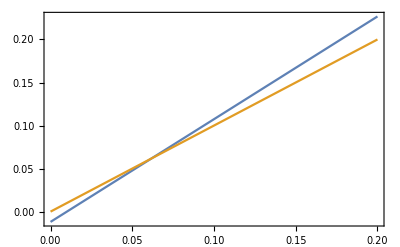

```mathematica
(* pobs -> prob. of observing a positive IGG/IGM result *)
(* ptrue -> prob. the tested person truly has the antibodies *)
pobs[ptrue_]:=ptrue(1-FNR-FPR)+FPR;
ptrue[pobs_]:=(pobs-FPR)/(1-FNR-FPR);
{ptrue[0],ptrue[1-FNR]}
Plot[{ptrue[pobs],pobs},{pobs,0,.2},Frame->True]
```

### P2σfun

```mathematica
(* Computes the max. likelihood and 95% CI using HDI *)
```

```mathematica
Clear[p2σstatesfun]
p2σstatesfun[post_,naivep_,minp_,maxp_]:=Module[{wprec=27},
{minpshort,maxpshort}={minp,Max[-3ptrue[0],naivep+(maxp-naivep)/3.]};
maxvalue=FindMaxValue[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec];
pmax=p/.FindMaximum[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec][[2]];
If[pmax==minpshort&&minpshort≠minp,Print["Error: minpshort too high! minpshort = "<>ToString[1.minpshort]]];
conflevel[pcut_]:=NIntegrate[post[p]HeavisideTheta[post[p]-pcut],{p,minp,maxp},Method->"LocalAdaptive",PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->wprec];
medianfun[x_?NumericQ]:=NIntegrate[post[p],{p,minp,x},Method->"LocalAdaptive",WorkingPrecision->wprec+5,PrecisionGoal->4,AccuracyGoal->4];
pmedian=x/.FindRoot[medianfun[x]==1/2,{x,(105/100)pmax},WorkingPrecision->wprec+5];
pcutvec=Range[maxvalue/100,maxvalue*5/10,maxvalue/90];
conffun=Interpolation[ParallelMap[{#,conflevel[#]}&,pcutvec]];
(*FindMinimum[(conffun[x]-0.95)^2,{x,3}]*)
pcut=x/.FindRoot[conffun[x]==95/100,{x,(1/10)conffun[[1,1,2]]},WorkingPrecision->wprec];
p2σmin=If[pmax==minp,minp,p/.FindRoot[post[p]==pcut,{p,Max[minp,(8/10)pmax],minp,pmax},WorkingPrecision->wprec]];
p2σmax=p/.FindRoot[post[p]==pcut,{p,(12/10)pmax,pmax,maxp},WorkingPrecision->wprec];
crosstest=NIntegrate[post[p],{p,p2σmin,p2σmax},WorkingPrecision->wprec,AccuracyGoal->5,PrecisionGoal->4];
If[crosstest>.955||crosstest<.945,Print["Error: 95% confidence level cross-check failed!"]];
{pmax,pmedian,p2σmin,p2σmax}+=ptrue[0]; (* displacement due to FPR *)
(*pmax=Max[pmax,0];p2σmin=Max[p2σmin,0];*)
Print[Round[{pmax,p2σmin,p2σmax,crosstest},10.^-4]];
{pmax,pmedian,p2σmin,p2σmax,crosstest}
];
```

```mathematica
p2σstatesexactfun[post_,naivep_,minp_,maxp_]:=Module[{wprec=27},
{minpshort,maxpshort}={minp,naivep+(maxp-naivep)/3.};
maxvalue=FindMaxValue[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec];
pmax=p/.FindMaximum[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec][[2]];
If[pmax==minpshort&&minpshort≠minp,Print["Error: minpshort too high! minpshort = "<>ToString[1.minpshort]]];
conflevel[pcut_]:=NIntegrate[post[p]HeavisideTheta[post[p]-pcut],{p,minp,maxp},Method->"LocalAdaptive",PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->wprec];
medianfun[x_?NumericQ]:=NIntegrate[post[p],{p,minp,x},Method->"LocalAdaptive",WorkingPrecision->wprec+5,PrecisionGoal->4,AccuracyGoal->4];
pmedian=x/.FindRoot[medianfun[x]==1/2,{x,(107/100)pmax+10^-5},WorkingPrecision->wprec+5];
(*pmedian=1;*)
pcutvec=Range[maxvalue/100,maxvalue*5/10,maxvalue/90];
conffun=Interpolation[ParallelMap[{#,conflevel[#]}&,pcutvec]];
(*FindMinimum[(conffun[x]-0.95)^2,{x,3}]*)
pcut=x/.FindRoot[conffun[x]==95/100,{x,(1/10)conffun[[1,1,2]]},WorkingPrecision->wprec];
p2σmin=If[pmax==minp,minp,p/.NMinimize[{(finalpost2[p]-pcut)^2,minp<p<pmax},p,WorkingPrecision->wprec][[2]]];
p2σmax=p/.NMinimize[{(finalpost2[p]-pcut)^2,3/4>p>pmax},p,WorkingPrecision->wprec][[2]];
crosstest=NIntegrate[post[p],{p,p2σmin,p2σmax},WorkingPrecision->wprec,AccuracyGoal->5,PrecisionGoal->4];
If[crosstest>.954||crosstest<.946,Print["Error: 95% confidence level cross-check failed!"]];
(*pmax=Max[pmax,0];p2σmin=Max[p2σmin,0];*)
Print[Round[{pmax,pmedian,p2σmin,p2σmax,crosstest},10.^-4]];
{pmax,pmedian,p2σmin,p2σmax,crosstest}
];
```

```mathematica
errorfun[ptab_]:=Module[{},
Table[
pmode=ptab[[i,1]];
δplusminus={pmode-ptab[[i,3]],ptab[[i,4]]-pmode};
Around[100pmode,100δplusminus]
,{i,1,Length[ptab]}]
]
errormedianfun[ptab_]:=Module[{},
Table[
pmedian=ptab[[i,2]];
δplusminus={pmedian-ptab[[i,3]],ptab[[i,4]]-pmedian};
Around[100pmedian,100δplusminus]
,{i,1,Length[ptab]}]
]
```

```mathematica
(* Allows up to 500 cities *)
pname=Table[ToExpression["p"<>ToString[i]],{i,500}];
```

#### Exp issue

```mathematica
(*(compiledExp[x_Integer]:= #[x])& @ Compile[{{x, _Integer}},Exp[x]];*)
(compiledExp[x_Real]:= #[x])& @ Compile[{{x, _Real}},Exp[x]];
(compiledExp[x_Complex]:= #[x])& @ Compile[{{x, _Complex}},Exp[x]];

bigExp[x_?MachineNumberQ]:= Exp[SetPrecision[x,$MachinePrecision]];

munderflowExp[x_]:=
With[{y=compiledExp[x] (* Machine evaluation *)},
If[
y==0 (* Condition for machine underflow *),
bigExp[x] (* Action to take on machine underflow converting to a bignum result *),
y (* Machine precision result when underflow does not occur *)
]
];

Unprotect[Exp];
Exp[x_?MachineNumberQ]:=munderflowExp[x];
Protect[Exp];

Log[Exp[-1000]]
Log[Exp[-1000.]]
```

-1000

-1000.

## Main Calculations - 1st round

```mathematica
CloseKernels[];
LaunchKernels[7];
```

```mathematica
datacities=datacities3rounds[[All,{1,2,3,6,-1}]];
```

### Combining states

```mathematica
datacities[[All,1]]
(*statesindex={1,3,5,9,11,15,19,20,23,28,31,39,41,42,48,49,54,60,63,64,65,66,74,80,82,88,91}*)
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]]
Dimensions[datastates]
datastates[[All,1,1]]
datastates[[1;;5]]
ncities=Table[Length[datastates[[i]]],{i,Length[datastates]}]
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{AC,AC,AL,AL,AM,AM,AM,AM,AP,AP,BA,BA,BA,BA,BA,BA,BA,BA,BA,BA,CE,CE,CE,CE,CE,CE,DF,ES,ES,ES,ES,GO,GO,GO,GO,GO,GO,MA,MA,MA,MA,MA,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MS,MS,MS,MT,MT,MT,MT,MT,PA,PA,PA,PA,PA,PA,PA,PB,PB,PB,PB,PE,PE,PE,PE,PI,PI,PI,PI,PI,PI,PR,PR,PR,PR,PR,PR,RJ,RJ,RJ,RJ,RJ,RN,RN,RN,RO,RO,RR,RR,RS,RS,RS,RS,RS,RS,RS,RS,SC,SC,SC,SC,SC,SC,SC,SE,SE,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,TO,TO,TO}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{27}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{{{AC,CRUZEIRO DO SUL,250,1,88376},{AC,RIO BRANCO,250,12,407319}},{{AL,ARAPIRACA,223,0,231747},{AL,MACEIÓ,234,3,1018948}},{{AM,LÁBREA,250,0,46069},{AM,MANAUS,250,27,2182763},{AM,PARINTINS,250,11,114273},{AM,TEFÉ,250,42,59849}},{{AP,MACAPÁ,250,21,503327},{AP,OIAPOQUE,250,8,27270}},{{BA,BARREIRAS,250,0,155439},{BA,FEIRA DE SANTANA,66,1,614872},{BA,GUANAMBI,245,0,84481},{BA,IRECÊ,41,0,72967},{BA,ITABUNA,60,0,213223},{BA,JUAZEIRO,250,0,216707},{BA,PAULO AFONSO,66,0,117782},{BA,SALVADOR,250,0,2872347},{BA,SANTO ANTÔNIO DE JESUS,86,0,101512},{BA,VITÓRIA DA CONQUISTA,86,0,338480}}}

{2,2,4,2,10,6,1,4,6,5,13,3,5,7,4,4,6,6,5,3,2,2,8,7,2,11,3}

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Total[datastates[[All,All,3]],{2}]
totround1=Total[%]
```

{500,457,1000,500,1400,1064,240,746,1305,894,2328,606,327,1513,272,371,1236,1459,866,372,423,401,1985,1631,500,1898,731}

25025

```mathematica
datastates2=datastates;
Table[datastates2[[i]]=Cases[datastates[[i]],_?( GreaterEqual[#[[3]],mintot]&)],{i,Length[datastates]}];
ncities2=Table[Length[datastates2[[i]]],{i,Length[datastates2]}]
Total[datastates2[[All,All,3]],{2}]
Total[%]
```

{2,2,4,2,4,4,1,3,5,3,8,2,1,6,0,1,5,6,3,1,1,1,8,6,2,6,3}

{500,457,1000,500,995,949,240,722,1128,750,1972,493,208,1479,0,240,1236,1459,689,229,250,250,1985,1439,500,1381,731}

21782

```mathematica
datastates//TableForm
```

AC
CRUZEIRO DO SUL
250
1
88376 | AC
RIO BRANCO
250
12
407319 |  |  |  |  |  |  |  |  |  |  | 
AL
ARAPIRACA
223
0
231747 | AL
MACEIÓ
234
3
1018948 |  |  |  |  |  |  |  |  |  |  | 
AM
LÁBREA
250
0
46069 | AM
MANAUS
250
27
2182763 | AM
PARINTINS
250
11
114273 | AM
TEFÉ
250
42
59849 |  |  |  |  |  |  |  |  | 
AP
MACAPÁ
250
21
503327 | AP
OIAPOQUE
250
8
27270 |  |  |  |  |  |  |  |  |  |  | 
BA
BARREIRAS
250
0
155439 | BA
FEIRA DE SANTANA
66
1
614872 | BA
GUANAMBI
245
0
84481 | BA
IRECÊ
41
0
72967 | BA
ITABUNA
60
0
213223 | BA
JUAZEIRO
250
0
216707 | BA
PAULO AFONSO
66
0
117782 | BA
SALVADOR
250
0
2872347 | BA
SANTO ANTÔNIO DE JESUS
86
0
101512 | BA
VITÓRIA DA CONQUISTA
86
0
338480 |  |  | 
CE
CRATEÚS
247
2
75074 | CE
FORTALEZA
225
17
2669342 | CE
IGUATU
9
0
102498 | CE
JUAZEIRO DO NORTE
106
0
274207 | CE
QUIXADÁ
245
0
87728 | CE
SOBRAL
232
4
208935 |  |  |  |  |  |  | 
DF
BRASÍLIA
240
0
3015268 |  |  |  |  |  |  |  |  |  |  |  | 
ES
CACHOEIRO DE ITAPEMIRIM
250
0
208972 | ES
COLATINA
222
0
122499 | ES
SÃO MATEUS
24
0
130611 | ES
VITÓRIA
250
3
362097 |  |  |  |  |  |  |  |  | 
GO
GOIÂNIA
235
0
1516113 | GO
IPORÁ
250
0
31531 | GO
ITUMBIARA
241
0
104742 | GO
LUZIÂNIA
177
0
208299 | GO
PORANGATU
200
0
45394 | GO
RIO VERDE
202
0
235647 |  |  |  |  |  |  | 
MA
BACABAL
250
2
104949 | MA
CAXIAS
250
0
164880 | MA
IMPERATRIZ
41
0
258682 | MA
PRESIDENTE DUTRA
250
1
47804 | MA
SÃO LUÍS
103
1
1101884 |  |  |  |  |  |  |  | 
MG
BARBACENA
56
0
137313 | MG
BELO HORIZONTE
168
0
2512070 | MG
DIVINÓPOLIS
16
0
238230 | MG
GOVERNADOR VALADARES
34
0
279885 | MG
IPATINGA
82
0
263410 | MG
JUIZ DE FORA
250
1
568873 | MG
MONTES CLAROS
250
0
409341 | MG
PATOS DE MINAS
250
1
152488 | MG
POUSO ALEGRE
250
0
150737 | MG
TEÓFILO OTONI
242
1
140592 | MG
UBERABA
250
0
333783 | MG
UBERLÂNDIA
235
0
691305 | MG
VARGINHA
245
0
135558
MS
CAMPO GRANDE
113
0
895982 | MS
CORUMBÁ
250
0
111435 | MS
DOURADOS
243
0
222949 |  |  |  |  |  |  |  |  |  | 
MT
BARRA DO GARÇAS
7
0
61012 | MT
CÁCERES
208
0
94376 | MT
CUIABÁ
86
0
612547 | MT
RONDONÓPOLIS
4
0
232491 | MT
SINOP
22
0
142996 |  |  |  |  |  |  |  | 
PA
ALTAMIRA
232
1
114594 | PA
BELÉM
247
32
1492745 | PA
BREVES
250
53
102701 | PA
CASTANHAL
250
33
200793 | PA
MARABÁ
250
18
279349 | PA
REDENÇÃO
250
0
84787 | PA
SANTARÉM
34
1
304589 |  |  |  |  |  | 
PB
CAMPINA GRANDE
39
0
409731 | PB
JOÃO PESSOA
180
0
809015 | PB
PATOS
42
0
107605 | PB
SOUSA
11
0
69444 |  |  |  |  |  |  |  |  | 
PE
CARUARU
39
0
361118 | PE
PETROLINA
66
0
349145 | PE
RECIFE
240
7
1645727 | PE
SERRA TALHADA
26
0
86350 |  |  |  |  |  |  |  |  | 
PI
CORRENTE
250
0
26644 | PI
FLORIANO
239
0
59935 | PI
PARNAÍBA
250
0
153078 | PI
PICOS
0
0
78222 | PI
SÃO RAIMUNDO NONATO
247
0
34710 | PI
TERESINA
250
1
864845 |  |  |  |  |  |  | 
PR
CASCAVEL
248
1
328454 | PR
CURITIBA
217
0
1933105 | PR
GUARAPUAVA
250
0
181504 | PR
LONDRINA
244
0
569733 | PR
MARINGÁ
250
0
423666 | PR
PONTA GROSSA
250
4
351736 |  |  |  |  |  |  | 
RJ
CAMPOS DOS GOYTACAZES
21
0
507548 | RJ
MACAÉ
156
1
256672 | RJ
PETRÓPOLIS
239
1
306191 | RJ
RIO DE JANEIRO
243
5
6718903 | RJ
VOLTA REDONDA
207
0
273012 |  |  |  |  |  |  |  | 
RN
CAICÓ
5
0
67952 | RN
MOSSORÓ
138
4
297378 | RN
NATAL
229
2
884122 |  |  |  |  |  |  |  |  |  | 
RO
JI-PARANÁ
250
0
128969 | RO
PORTO VELHO
173
1
529544 |  |  |  |  |  |  |  |  |  |  | 
RR
BOA VISTA
250
10
399213 | RR
RORAINÓPOLIS
151
1
30163 |  |  |  |  |  |  |  |  |  |  | 
RS
CAXIAS DO SUL
250
0
510906 | RS
IJUÍ
240
0
83475 | RS
PASSO FUNDO
250
1
203275 | RS
PELOTAS
247
0
342405 | RS
PORTO ALEGRE
248
0
1483771 | RS
SANTA CRUZ DO SUL
250
0
130416 | RS
SANTA MARIA
250
0
282123 | RS
URUGUAIANA
250
0
126970 |  |  |  |  | 
SC
BLUMENAU
232
0
357199 | SC
CAÇADOR
192
0
78595 | SC
CHAPECÓ
250
0
220367 | SC
CRICIÚMA
250
0
215186 | SC
FLORIANÓPOLIS
223
1
500973 | SC
JOINVILLE
250
0
590466 | SC
LAGES
234
0
157544 |  |  |  |  |  | 
SE
ARACAJU
250
1
657013 | SE
ITABAIANA
250
0
95427 |  |  |  |  |  |  |  |  |  |  | 
SP
ARAÇATUBA
190
0
197016 | SP
ARARAQUARA
121
0
236072 | SP
BAURU
225
0
376818 | SP
CAMPINAS
237
2
1204073 | SP
MARÍLIA
229
0
238882 | SP
PRESIDENTE PRUDENTE
116
0
228743 | SP
RIBEIRÃO PRETO
239
1
703293 | SP
SÃO JOSÉ DO RIO PRETO
239
0
460671 | SP
SÃO JOSÉ DOS CAMPOS
51
0
721944 | SP
SÃO PAULO
212
6
12252023 | SP
SOROCABA
39
0
679378 |  | 
TO
ARAGUAÍNA
238
0
180470 | TO
GURUPI
250
0
86647 | TO
PALMAS
243
0
299127 |  |  |  |  |  |  |  |  |  |

```mathematica
datastates[[12]]
```

{{MS,CAMPO GRANDE,113,0,895982},{MS,CORUMBÁ,250,0,111435},{MS,DOURADOS,243,0,222949}}

### Exact Code

```mathematica
ilist=Sort[Join[ilist,{10,13}]]
```

{1,2,3,4,7,8,10,12,13,15,16,20,21,22,25,27}

```mathematica
ilist=Flatten[Position[ncities,n_ /; 5<n<7],1]
```

{6,9,17,18}

```mathematica
CloseKernels[];
LaunchKernels[3];
```

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
Clear[ntot,nyes,finalpost,jointpost,pvec]
AbsoluteTiming[Monitor[ptabstatesRound1exact=
Table[
tab=Table[
ntot=datastates[[i,j,3]];
nyes=datastates[[i,j,4]];
post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
(*norm=NIntegrate[posttest[p],{p,0,1},AccuracyGoal->9,WorkingPrecision->28];
post[p_]=post[p]/norm;*)
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
(*NIntegrate[postcorr[p],{p,ptrue[0],ptrue[1]}];*)
norm2=NIntegrate[postcorr[p],{p,0,1},AccuracyGoal->9+1,WorkingPrecision->30+20]; (* Must be one *)
postcorr[p_]=postcorr[p]/norm2
,{j,1,Length[datastates[[i]]]}];

popstate=Total[datastates[[i,All,5]]];
fracpop=datastates[[i,All,5]]/popstate;
ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

vartab=Table[vari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
μjoint=meantab.fracpop;
{minp,maxp,dp}={Max[1/1000000,μjoint-6 √varjoint],Min[1,μjoint+7 √varjoint],(11 √varjoint)/105};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

pvec=pname[[1;;Length[tab]]];
jointpost[pvec_]=Module[{aux=1},
Do[aux*=(tab[[j]]/.p->pname[[j]]);,{j,Length[tab]}];
aux];
delta[pvec_]:=Sum[pname[[j]] fracpop[[j]],{j,Length[pvec]}];
norma[pvec_]:=Norm[Table[D[delta[pvec], pname[[j]]],{j,Length[pvec]}]];
logicfun[pvec_]:=Apply[And,Flatten[Table[{GreaterEqual[pvec[[j]],0],LessEqual[pvec[[j]],1]},{j,Length[pvec]}]]];
reg[p_]=ImplicitRegion[p==delta[pvec]∧logicfun[pvec],Evaluate[pvec]];
If[i==19,finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->35,PrecisionGoal->4,WorkingPrecision->39];,
finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->6+0,PrecisionGoal->4+0,WorkingPrecision->26+2];];

finalposttab=ParallelMap[{#,finalpost[#]}&,Range[minp,maxp+dp,dp]];
finalpost2=Interpolation[finalposttab,InterpolationOrder->3];
Print[i];
(*finalpost[p_]:=NIntegrate[jointpost[{p1,p2}]/norma[p1,p2],{p1,p2}∈reg[p],AccuracyGoal->9-2,WorkingPrecision->28-4];*)
ntot=Total[datastates[[i,All,3]]];
nyes=Total[datastates[[i,All,4]]];
NotebookSave[];
result=p2σstatesexactfun[finalpost2,μjoint(2/3),minp,maxp];
Prepend[result,i]
,{i,10,10(*ilist*)}];
,{i,ntot,nyes,1.μjoint,popstate,result[[2]],1.minp,1.maxp}]]
1.minp
ParallelEvaluate[On[NIntegrate::ncvb]];
ParallelEvaluate[On[NIntegrate::slwcon]];
```

10

{0.0092,0.0141,0.0013,0.0379,0.95}

{637.635,Null}

1.×10^-6

### BetaDistribution Code

For a given city: 
mean → mean + ptrue[0]  (which is smaller than mean) and multiplied by (1/norm2)
variance is multiplied by (1/norm2)^2

```mathematica
ptabstatesRound1exact=Import[dir<>"prob-tab-states-round1-exact-v1.csv","CSV"];
Dimensions[ptabstatesRound1exact]
ptabstatesRound1exact[[1]]
```

{18,6}

{1,0.047651851053319897774797243,1,0.02612982867052724643055762,0.078084495622938248333990314,0.950000011137750126703072}

```mathematica
CloseKernels[];
LaunchKernels[2];
```

```mathematica
(* NEW *)
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
Clear[ptabstatesRound1,ntot,nyes]
AbsoluteTiming[Monitor[ptabstatesRound1=
Table[
length=Length[datastates[[i]]];

popstate=Total[datastates[[i,All,-1]]];
fracpop=datastates[[i,All,-1]]/popstate;

meanvartab=Table[newmeanvari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,length}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{minp,maxp,dp}={Max[-ptrue[0]/(ptrue[1]+ptrue[0])^0,μjoint-5 √varjoint],Min[1,μjoint+8 √varjoint],3*(11 √varjoint)/(56*3)};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint,V->varjoint};
norm3=1/NIntegrate[beta[p,bestα,bestβ],{p,minp,maxp},WorkingPrecision->34];

(* Does a 2nd iteration since norm3 affects the mean and variance *)
{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint/norm3^(3/2),V->varjoint/norm3^-1};
norm3=1/NIntegrate[beta[p,bestα,bestβ],{p,minp,maxp},WorkingPrecision->34];

finalpostbeta[p_]:=norm3 beta[p,bestα,bestβ];

ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];
result=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),minp,maxp];
Join[result,Round[{bestα,bestβ},N[{bestα,bestβ},9]],{Round[√varjoint,10.^-7]}]
,{i,1,Length[datastates]}];
,{i,ntot,nyes,1. bestα/(bestα+bestβ),popstate}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
```

{0.430842,Null}

```mathematica
norm3
Round[ptabstatesRound1,.00001]
```

1.537651214906480500102050217456042

{{0.00066,0.00401,0.,0.01241,0.95,8.49601,588.867,0.00484}}

```mathematica
Export["prob-tab-states-FPR1.00%-round1-v4.csv",Round[ptabstatesRound1,10.^-4],"CSV"]
```

prob-tab-states-FPR1.00%-round1-v4.csv

### Whole country

{11.7841,Null}

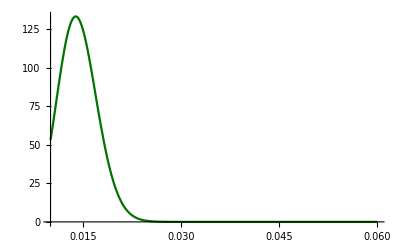

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
AbsoluteTiming[
popstate=Total[datacities[[All,-1]]];

fracpop=datacities[[All,-1]]/popstate;

naivep=fracpop.(datacities[[All,4]]/(datacities[[All,3]]+1)); (* +1 to avoid error due to cities with 0 tests *)
{minp,maxp}=Rationalize[{Max[0,naivep-7/100],Min[1,naivep+8/100]},10^-4];

(*vartab=Table[vari[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
μjoint=meantab.fracpop;*)

meanvartab=Table[newmeanvari[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop+ptrue[0];
varjoint= vartab.fracpop^2;

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint,V->varjoint};
finalpostbeta[p_]:=beta[p,bestα,bestβ];
]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazilround1=Plot[finalpostbeta[p-ptrue[0]],{p,.01,.06},PlotRange->All,PlotStyle->Darker[Green,.55]]
```

```mathematica
1.μjoint
√varjoint
```

0.0261177

0.00300523985722082889678616942947

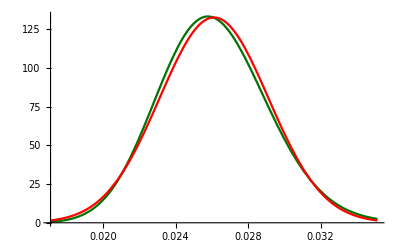

```mathematica
Plot[{finalpostbeta[p-0ptrue[0]],PDF[NormalDistribution[μjoint+0ptrue[0],√varjoint],p]},{p,μjoint-3 √varjoint+0ptrue[0],μjoint+3 √varjoint+0ptrue[0]},PlotRange->All,PlotStyle->{Darker[Green,.55],Red}]
```

```mathematica
FindMaximum[finalpostbeta[p],{p,.025}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{133.413,{p→0.0257808}}

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound1=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint,μjoint+4 √varjoint]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil1=Round[Join[ptabBrazilRound1,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound1=errorfun[{ptabBrazilRound1[[1;;4]]}][[1]]
```

$Aborted

Round[Join[ptabBrazilRound1,{73.5299803154371008622632955041,2741.79932002229186191712559629,0.00300523985722082889678616942947}],0.0001]

Part::take: Cannot take positions 1 through 4 in ptabBrazilRound1.

Part::partw: Part 3 of ptabBrazilRound1⟦1;;4⟧ does not exist.

Part::partw: Part 4 of ptabBrazilRound1⟦1;;4⟧ does not exist.

100 ptabBrazilRound1100 (ptabBrazilRound1-{ptabBrazilRound1⟦1;;4⟧}⟦1,3⟧)100 (-ptabBrazilRound1+{ptabBrazilRound1⟦1;;4⟧}⟦1,4⟧)

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound1=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint,μjoint+4 √varjoint]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil1=Round[Join[ptabBrazilRound1,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound1=errorfun[{ptabBrazilRound1[[1;;4]]}][[1]]
```

{0.0259,0.0203,0.0321,0.95}

{0.025889586828404822713632902,0.02604175987111395627704368390697,0.020302526585972560319275438,0.032061213590668353386979851,0.949999993939129850733869567}

{0.0259,0.026,0.0203,0.0321,0.95,154.176,3897.66,0.003}

2.60.60.6

```mathematica
pmin2=x/.FindRoot[CDF[BetaDistribution[bestα,bestβ],x-ptrue[0]]==.05,{x,.01,.02},AccuracyGoal->11,PrecisionGoal->11]
pmax2=x/.FindRoot[CDF[BetaDistribution[bestα,bestβ],x-ptrue[0]]==.95,{x,.02,.03},AccuracyGoal->11,PrecisionGoal->11]
NIntegrate[finalpostbeta[p-ptrue[0]],{p,pmin2,pmax2},WorkingPrecision->25,AccuracyGoal->11,PrecisionGoal->11]
```

0.0146885

0.0246585

0.8999999999994840519821754

## Main Calculations - 2nd round

```mathematica
datacities=datacities3rounds[[All,{1,2,4,7,-1}]];
```

### Combining states

```mathematica
datacities=datacities3rounds[[All,{1,2,4,7,-1}]];
datacities[[All,1]]
(*statesindex={1,3,5,9,11,15,19,20,23,28,31,39,41,42,48,49,54,60,63,64,65,66,74,80,82,88,91}*)
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]];
Dimensions[datastates]
datastates[[All,1,1]]
datastates[[1;;5]]
ncities=Table[Length[datastates[[i]]],{i,Length[datastates]}]
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{AC,AC,AL,AL,AM,AM,AM,AM,AP,AP,BA,BA,BA,BA,BA,BA,BA,BA,BA,BA,CE,CE,CE,CE,CE,CE,DF,ES,ES,ES,ES,GO,GO,GO,GO,GO,GO,MA,MA,MA,MA,MA,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MS,MS,MS,MT,MT,MT,MT,MT,PA,PA,PA,PA,PA,PA,PA,PB,PB,PB,PB,PE,PE,PE,PE,PI,PI,PI,PI,PI,PI,PR,PR,PR,PR,PR,PR,RJ,RJ,RJ,RJ,RJ,RN,RN,RN,RO,RO,RR,RR,RS,RS,RS,RS,RS,RS,RS,RS,SC,SC,SC,SC,SC,SC,SC,SE,SE,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,TO,TO,TO}

{27}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{{{AC,CRUZEIRO DO SUL,250,33,88376},{AC,RIO BRANCO,250,10,407319}},{{AL,ARAPIRACA,250,6,231747},{AL,MACEIÓ,250,26,1018948}},{{AM,LÁBREA,250,8,46069},{AM,MANAUS,250,31,2182763},{AM,PARINTINS,250,24,114273},{AM,TEFÉ,250,43,59849}},{{AP,MACAPÁ,250,32,503327},{AP,OIAPOQUE,250,11,27270}},{{BA,BARREIRAS,250,0,155439},{BA,FEIRA DE SANTANA,208,1,614872},{BA,GUANAMBI,250,0,84481},{BA,IRECÊ,250,0,72967},{BA,ITABUNA,200,1,213223},{BA,JUAZEIRO,250,0,216707},{BA,PAULO AFONSO,250,1,117782},{BA,SALVADOR,215,10,2872347},{BA,SANTO ANTÔNIO DE JESUS,0,0,101512},{BA,VITÓRIA DA CONQUISTA,250,0,338480}}}

{2,2,4,2,10,6,1,4,6,5,13,3,5,7,4,4,6,6,5,3,2,2,8,7,2,11,3}

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Total[datastates[[All,All,3]],{2}]
totround2=Total[%]
```

{500,500,1000,500,2123,1402,250,1000,1500,1232,3163,703,1112,1750,1000,942,1500,1094,1145,603,500,500,1881,1594,500,2471,700}

31165

```mathematica
datastates//TableForm
```

AC
CRUZEIRO DO SUL
250
33
88376 | AC
RIO BRANCO
250
10
407319 |  |  |  |  |  |  |  |  |  |  | 
AL
ARAPIRACA
250
6
231747 | AL
MACEIÓ
250
26
1018948 |  |  |  |  |  |  |  |  |  |  | 
AM
LÁBREA
250
8
46069 | AM
MANAUS
250
31
2182763 | AM
PARINTINS
250
24
114273 | AM
TEFÉ
250
43
59849 |  |  |  |  |  |  |  |  | 
AP
MACAPÁ
250
32
503327 | AP
OIAPOQUE
250
11
27270 |  |  |  |  |  |  |  |  |  |  | 
BA
BARREIRAS
250
0
155439 | BA
FEIRA DE SANTANA
208
1
614872 | BA
GUANAMBI
250
0
84481 | BA
IRECÊ
250
0
72967 | BA
ITABUNA
200
1
213223 | BA
JUAZEIRO
250
0
216707 | BA
PAULO AFONSO
250
1
117782 | BA
SALVADOR
215
10
2872347 | BA
SANTO ANTÔNIO DE JESUS
0
0
101512 | BA
VITÓRIA DA CONQUISTA
250
0
338480 |  |  | 
CE
CRATEÚS
250
2
75074 | CE
FORTALEZA
226
30
2669342 | CE
IGUATU
250
2
102498 | CE
JUAZEIRO DO NORTE
250
3
274207 | CE
QUIXADÁ
250
3
87728 | CE
SOBRAL
176
33
208935 |  |  |  |  |  |  | 
DF
BRASÍLIA
250
2
3015268 |  |  |  |  |  |  |  |  |  |  |  | 
ES
CACHOEIRO DE ITAPEMIRIM
250
3
208972 | ES
COLATINA
250
2
122499 | ES
SÃO MATEUS
250
0
130611 | ES
VITÓRIA
250
7
362097 |  |  |  |  |  |  |  |  | 
GO
GOIÂNIA
250
0
1516113 | GO
IPORÁ
250
0
31531 | GO
ITUMBIARA
250
0
104742 | GO
LUZIÂNIA
250
3
208299 | GO
PORANGATU
250
0
45394 | GO
RIO VERDE
250
1
235647 |  |  |  |  |  |  | 
MA
BACABAL
250
10
104949 | MA
CAXIAS
250
1
164880 | MA
IMPERATRIZ
250
35
258682 | MA
PRESIDENTE DUTRA
250
18
47804 | MA
SÃO LUÍS
232
13
1101884 |  |  |  |  |  |  |  | 
MG
BARBACENA
250
0
137313 | MG
BELO HORIZONTE
250
0
2512070 | MG
DIVINÓPOLIS
250
0
238230 | MG
GOVERNADOR VALADARES
189
1
279885 | MG
IPATINGA
224
0
263410 | MG
JUIZ DE FORA
250
0
568873 | MG
MONTES CLAROS
250
0
409341 | MG
PATOS DE MINAS
250
0
152488 | MG
POUSO ALEGRE
250
0
150737 | MG
TEÓFILO OTONI
250
2
140592 | MG
UBERABA
250
0
333783 | MG
UBERLÂNDIA
250
0
691305 | MG
VARGINHA
250
0
135558
MS
CAMPO GRANDE
203
0
895982 | MS
CORUMBÁ
250
0
111435 | MS
DOURADOS
250
1
222949 |  |  |  |  |  |  |  |  |  | 
MT
BARRA DO GARÇAS
250
1
61012 | MT
CÁCERES
215
0
94376 | MT
CUIABÁ
250
3
612547 | MT
RONDONÓPOLIS
147
2
232491 | MT
SINOP
250
0
142996 |  |  |  |  |  |  |  | 
PA
ALTAMIRA
250
6
114594 | PA
BELÉM
250
36
1492745 | PA
BREVES
250
26
102701 | PA
CASTANHAL
250
23
200793 | PA
MARABÁ
250
22
279349 | PA
REDENÇÃO
250
3
84787 | PA
SANTARÉM
250
23
304589 |  |  |  |  |  | 
PB
CAMPINA GRANDE
250
14
409731 | PB
JOÃO PESSOA
250
13
809015 | PB
PATOS
250
3
107605 | PB
SOUSA
250
2
69444 |  |  |  |  |  |  |  |  | 
PE
CARUARU
222
4
361118 | PE
PETROLINA
250
0
349145 | PE
RECIFE
220
6
1645727 | PE
SERRA TALHADA
250
2
86350 |  |  |  |  |  |  |  |  | 
PI
CORRENTE
250
0
26644 | PI
FLORIANO
250
0
59935 | PI
PARNAÍBA
250
12
153078 | PI
PICOS
250
1
78222 | PI
SÃO RAIMUNDO NONATO
250
0
34710 | PI
TERESINA
250
3
864845 |  |  |  |  |  |  | 
PR
CASCAVEL
250
0
328454 | PR
CURITIBA
123
0
1933105 | PR
GUARAPUAVA
250
0
181504 | PR
LONDRINA
111
0
569733 | PR
MARINGÁ
126
0
423666 | PR
PONTA GROSSA
234
0
351736 |  |  |  |  |  |  | 
RJ
CAMPOS DOS GOYTACAZES
189
2
507548 | RJ
MACAÉ
206
1
256672 | RJ
PETRÓPOLIS
250
1
306191 | RJ
RIO DE JANEIRO
250
16
6718903 | RJ
VOLTA REDONDA
250
1
273012 |  |  |  |  |  |  |  | 
RN
CAICÓ
250
0
67952 | RN
MOSSORÓ
112
6
297378 | RN
NATAL
241
7
884122 |  |  |  |  |  |  |  |  |  | 
RO
JI-PARANÁ
250
2
128969 | RO
PORTO VELHO
250
7
529544 |  |  |  |  |  |  |  |  |  |  | 
RR
BOA VISTA
250
54
399213 | RR
RORAINÓPOLIS
250
22
30163 |  |  |  |  |  |  |  |  |  |  | 
RS
CAXIAS DO SUL
250
0
510906 | RS
IJUÍ
176
1
83475 | RS
PASSO FUNDO
233
1
203275 | RS
PELOTAS
250
0
342405 | RS
PORTO ALEGRE
230
0
1483771 | RS
SANTA CRUZ DO SUL
250
0
130416 | RS
SANTA MARIA
242
0
282123 | RS
URUGUAIANA
250
0
126970 |  |  |  |  | 
SC
BLUMENAU
239
1
357199 | SC
CAÇADOR
250
0
78595 | SC
CHAPECÓ
250
0
220367 | SC
CRICIÚMA
185
0
215186 | SC
FLORIANÓPOLIS
205
0
500973 | SC
JOINVILLE
250
0
590466 | SC
LAGES
215
0
157544 |  |  |  |  |  | 
SE
ARACAJU
250
2
657013 | SE
ITABAIANA
250
3
95427 |  |  |  |  |  |  |  |  |  |  | 
SP
ARAÇATUBA
250
1
197016 | SP
ARARAQUARA
247
0
236072 | SP
BAURU
250
1
376818 | SP
CAMPINAS
250
1
1204073 | SP
MARÍLIA
250
0
238882 | SP
PRESIDENTE PRUDENTE
250
0
228743 | SP
RIBEIRÃO PRETO
250
0
703293 | SP
SÃO JOSÉ DO RIO PRETO
94
0
460671 | SP
SÃO JOSÉ DOS CAMPOS
170
0
721944 | SP
SÃO PAULO
250
5
12252023 | SP
SOROCABA
210
1
679378 |  | 
TO
ARAGUAÍNA
200
2
180470 | TO
GURUPI
250
0
86647 | TO
PALMAS
250
1
299127 |  |  |  |  |  |  |  |  |  |

### Exact Code

```mathematica
CloseKernels[];
LaunchKernels[19];
```

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
Clear[ntot,nyes,finalpost,jointpost,pvec]
AbsoluteTiming[Monitor[ptabstatesRound2exact=
Table[
tab=Table[
ntot=datastates[[i,j,3]];
nyes=datastates[[i,j,4]];
post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
(*norm=NIntegrate[posttest[p],{p,0,1},AccuracyGoal->9,WorkingPrecision->28];
post[p_]=post[p]/norm;*)
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
(*NIntegrate[postcorr[p],{p,ptrue[0],ptrue[1]}];*)
norm2=NIntegrate[postcorr[p],{p,0,1},AccuracyGoal->9+1,WorkingPrecision->30+20]; (* Must be one *)
postcorr[p_]=postcorr[p]/norm2
,{j,1,Length[datastates[[i]]]}];

popstate=Total[datastates[[i,All,5]]];
fracpop=datastates[[i,All,5]]/popstate;
ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

vartab=Table[vari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
μjoint=meantab.fracpop;
{minp,maxp,dp}={Max[1/1000000,μjoint-6 √varjoint],Min[1,μjoint+7 √varjoint],(11 √varjoint)/105};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

pvec=pname[[1;;Length[tab]]];
jointpost[pvec_]=Module[{aux=1},
Do[aux*=(tab[[j]]/.p->pname[[j]]);,{j,Length[tab]}];
aux];
delta[pvec_]:=Sum[pname[[j]] fracpop[[j]],{j,Length[pvec]}];
norma[pvec_]:=Norm[Table[D[delta[pvec], pname[[j]]],{j,Length[pvec]}]];
logicfun[pvec_]:=Apply[And,Flatten[Table[{GreaterEqual[pvec[[j]],0],LessEqual[pvec[[j]],1]},{j,Length[pvec]}]]];
reg[p_]=ImplicitRegion[p==delta[pvec]∧logicfun[pvec],Evaluate[pvec]];
If[i==19,finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->35,PrecisionGoal->4,WorkingPrecision->39];,
finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->6+0,PrecisionGoal->4+0,WorkingPrecision->26+2];];

finalposttab=ParallelMap[{#,finalpost[#]}&,Range[minp,maxp+dp,dp]];
finalpost2=Interpolation[finalposttab,InterpolationOrder->3];
Print[i];
(*finalpost[p_]:=NIntegrate[jointpost[{p1,p2}]/norma[p1,p2],{p1,p2}∈reg[p],AccuracyGoal->9-2,WorkingPrecision->28-4];*)
ntot=Total[datastates[[i,All,3]]];
nyes=Total[datastates[[i,All,4]]];
NotebookSave[];
result=p2σstatesexactfun[finalpost2,μjoint(2/3),minp,maxp];
Prepend[result,i]
,{i,3,3(*ilist*)}];
,{i,ntot,nyes,1.μjoint,popstate,result[[2]],1.minp,1.maxp}]]
1.minp
ParallelEvaluate[On[NIntegrate::ncvb]];
ParallelEvaluate[On[NIntegrate::slwcon]];
```

3

{0.074,0.0765,0.0447,0.1128,0.95}

{588.276,Null}

1.×10^-6

```mathematica
Round[result,.000001]
```

{0.074004,0.076469,0.044733,0.112752,0.95}

```mathematica
Export["prob-tab-states-round2-exact-v2.csv",Round[ptabstatesRound2exact,.00001],"CSV"]
```

prob-tab-states-round2-exact-v2.csv

```mathematica
NotebookSave[]
```

### BetaDistribution Code

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
Clear[ptabstatesRound2,ntot,nyes]
AbsoluteTiming[Monitor[ptabstatesRound2=
Table[
length=Length[datastates[[i]]];

popstate=Total[datastates[[i,All,-1]]];
fracpop=datastates[[i,All,-1]]/popstate;

meanvartab=Table[newmeanvari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,length}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{minp,maxp,dp}={Max[-ptrue[0]/(ptrue[1]+ptrue[0])^0,μjoint-5 √varjoint],Min[1,μjoint+8 √varjoint],3*(11 √varjoint)/(56*3)};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint,V->varjoint};
norm3=1/NIntegrate[beta[p,bestα,bestβ],{p,minp,maxp},WorkingPrecision->34];

(* Does a 2nd iteration since norm3 affects the mean and variance *)
(*{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint/norm3,V->varjoint/norm3};*)
{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint/norm3^(3/2),V->varjoint/norm3^-1};
norm3=1/NIntegrate[beta[p,bestα,bestβ],{p,minp,maxp},WorkingPrecision->34];

finalpostbeta[p_]:=norm3 beta[p,bestα,bestβ];

ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];
result=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),minp,maxp];
Join[result,Round[{bestα,bestβ},N[{bestα,bestβ},9]],{Round[√varjoint,10.^-7]}]
,{i,1,Length[datastates]}];
,{i,ntot,nyes,1. bestα/(bestα+bestβ),popstate}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
```

{0.0572,0.0343,0.0859,0.95}

{0.0954,0.0625,0.1356,0.95}

{0.1343,0.0943,0.1815,0.95}

{0.1359,0.0938,0.1859,0.95}

{0.0392,0.019,0.0662,0.95}

{0.1293,0.0919,0.1732,0.95}

{0.0014,0.,0.02,0.95}

{0.0146,0.0043,0.0283,0.95}

{0.0034,0.,0.0106,0.95}

{0.0668,0.0444,0.094,0.95}

{0.0045,0.0007,0.0089,0.95}

{0.0024,0.,0.0124,0.95}

{0.0085,0.0004,0.0193,0.95}

{0.1292,0.1005,0.1615,0.95}

{0.0481,0.0288,0.0722,0.95}

{0.018,0.0035,0.0392,0.95}

{0.0129,0.0028,0.0266,0.95}

{0.0062,0.,0.017,0.95}

{0.0552,0.0293,0.0894,0.95}

{0.0315,0.013,0.057,0.95}

{0.0192,0.0033,0.043,0.95}

{0.2354,0.1833,0.2928,0.95}

{0.0043,0.0001,0.0093,0.9499}

{0.005,0.001,0.0098,0.95}

{0.0039,0.,0.0183,0.95}

{0.0112,0.,0.0277,0.9502}

{0.0055,0.,0.0141,0.95}

{3973.9,Null}

### Whole country

{12.6409,Null}

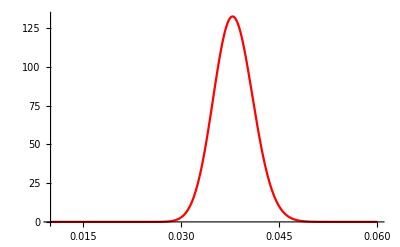

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
AbsoluteTiming[
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;
naivep=fracpop.(datacities[[All,4]]/(datacities[[All,3]]+1)); (* +1 to avoid error due to cities with 0 tests *)
{minp,maxp}=Rationalize[{Max[0,naivep-7/100],Min[1,naivep+8/100]},10^-4];

meanvartab=Table[newmeanvari[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint,V->varjoint};
finalpostbeta[p_]:=beta[p,bestα,bestβ];
]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazilround2=Plot[finalpostbeta[p-ptrue[0]],{p,.01,.06},PlotRange->All,PlotStyle->Red]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound2=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint,μjoint+4 √varjoint]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil2=Round[Join[ptabBrazilRound2,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound2=errorfun[{ptabBrazilRound2[[1;;4]]}][[1]]
```

{0.0378,0.0322,0.044,0.95}

{0.037839576983974360817800725,0.03795427439002521509937066481065,0.032167258172043173472564692,0.04395230406484412821026818,0.949999993799930319350987185}

{0.0378,0.038,0.0322,0.044,0.95,261.592,4976.05,0.003}

3.80.60.6

## Main Calculations - 3rd round

```mathematica
CloseKernels[];
LaunchKernels[7];
```

```mathematica
datacities=datacities3rounds[[All,{1,2,5,8,-1}]];
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]];
```

### Combining states

```mathematica
datacities=datacities3rounds[[All,{1,2,5,8,-1}]];
datacities[[All,1]]
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]];
Dimensions[datastates]
datastates[[All,1,1]]
datastates[[1;;5]]
ncities=Table[Length[datastates[[i]]],{i,Length[datastates]}]
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{AC,AC,AL,AL,AM,AM,AM,AM,AP,AP,BA,BA,BA,BA,BA,BA,BA,BA,BA,BA,CE,CE,CE,CE,CE,CE,DF,ES,ES,ES,ES,GO,GO,GO,GO,GO,GO,MA,MA,MA,MA,MA,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MS,MS,MS,MT,MT,MT,MT,MT,PA,PA,PA,PA,PA,PA,PA,PB,PB,PB,PB,PE,PE,PE,PE,PI,PI,PI,PI,PI,PI,PR,PR,PR,PR,PR,PR,RJ,RJ,RJ,RJ,RJ,RN,RN,RN,RO,RO,RR,RR,RS,RS,RS,RS,RS,RS,RS,RS,SC,SC,SC,SC,SC,SC,SC,SE,SE,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,TO,TO,TO}

{27}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{{{AC,CRUZEIRO DO SUL,250,28,88376},{AC,RIO BRANCO,250,9,407319}},{{AL,ARAPIRACA,250,11,231747},{AL,MACEIÓ,250,34,1018948}},{{AM,LÁBREA,250,17,46069},{AM,MANAUS,250,17,2182763},{AM,PARINTINS,250,26,114273},{AM,TEFÉ,250,37,59849}},{{AP,MACAPÁ,250,31,503327},{AP,OIAPOQUE,250,12,27270}},{{BA,BARREIRAS,250,1,155439},{BA,FEIRA DE SANTANA,250,5,614872},{BA,GUANAMBI,250,0,84481},{BA,IRECÊ,250,0,72967},{BA,ITABUNA,250,8,213223},{BA,JUAZEIRO,250,10,216707},{BA,PAULO AFONSO,211,2,117782},{BA,SALVADOR,250,8,2872347},{BA,SANTO ANTÔNIO DE JESUS,250,3,101512},{BA,VITÓRIA DA CONQUISTA,250,0,338480}}}

{2,2,4,2,10,6,1,4,6,5,13,3,5,7,4,4,6,6,5,3,2,2,8,7,2,11,3}

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Total[datastates[[All,All,3]],{2}]
totround3=Total[%]
```

{500,500,1000,500,2461,1500,250,1000,1500,1250,3250,750,1250,1750,1000,1000,1500,1500,1250,750,500,500,2000,1750,496,2750,750}

33207

```mathematica
datastates//TableForm
```

AC
CRUZEIRO DO SUL
250
28
88376 | AC
RIO BRANCO
250
9
407319 |  |  |  |  |  |  |  |  |  |  | 
AL
ARAPIRACA
250
11
231747 | AL
MACEIÓ
250
34
1018948 |  |  |  |  |  |  |  |  |  |  | 
AM
LÁBREA
250
17
46069 | AM
MANAUS
250
17
2182763 | AM
PARINTINS
250
26
114273 | AM
TEFÉ
250
37
59849 |  |  |  |  |  |  |  |  | 
AP
MACAPÁ
250
31
503327 | AP
OIAPOQUE
250
12
27270 |  |  |  |  |  |  |  |  |  |  | 
BA
BARREIRAS
250
1
155439 | BA
FEIRA DE SANTANA
250
5
614872 | BA
GUANAMBI
250
0
84481 | BA
IRECÊ
250
0
72967 | BA
ITABUNA
250
8
213223 | BA
JUAZEIRO
250
10
216707 | BA
PAULO AFONSO
211
2
117782 | BA
SALVADOR
250
8
2872347 | BA
SANTO ANTÔNIO DE JESUS
250
3
101512 | BA
VITÓRIA DA CONQUISTA
250
0
338480 |  |  | 
CE
CRATEÚS
250
10
75074 | CE
FORTALEZA
250
43
2669342 | CE
IGUATU
250
5
102498 | CE
JUAZEIRO DO NORTE
250
15
274207 | CE
QUIXADÁ
250
19
87728 | CE
SOBRAL
250
56
208935 |  |  |  |  |  |  | 
DF
BRASÍLIA
250
2
3015268 |  |  |  |  |  |  |  |  |  |  |  | 
ES
CACHOEIRO DE ITAPEMIRIM
250
7
208972 | ES
COLATINA
250
4
122499 | ES
SÃO MATEUS
250
3
130611 | ES
VITÓRIA
250
10
362097 |  |  |  |  |  |  |  |  | 
GO
GOIÂNIA
250
3
1516113 | GO
IPORÁ
250
1
31531 | GO
ITUMBIARA
250
1
104742 | GO
LUZIÂNIA
250
6
208299 | GO
PORANGATU
250
0
45394 | GO
RIO VERDE
250
4
235647 |  |  |  |  |  |  | 
MA
BACABAL
250
24
104949 | MA
CAXIAS
250
13
164880 | MA
IMPERATRIZ
250
31
258682 | MA
PRESIDENTE DUTRA
250
23
47804 | MA
SÃO LUÍS
250
13
1101884 |  |  |  |  |  |  |  | 
MG
BARBACENA
250
0
137313 | MG
BELO HORIZONTE
250
2
2512070 | MG
DIVINÓPOLIS
250
0
238230 | MG
GOVERNADOR VALADARES
250
2
279885 | MG
IPATINGA
250
1
263410 | MG
JUIZ DE FORA
250
0
568873 | MG
MONTES CLAROS
250
0
409341 | MG
PATOS DE MINAS
250
0
152488 | MG
POUSO ALEGRE
250
2
150737 | MG
TEÓFILO OTONI
250
5
140592 | MG
UBERABA
250
1
333783 | MG
UBERLÂNDIA
250
1
691305 | MG
VARGINHA
250
1
135558
MS
CAMPO GRANDE
250
1
895982 | MS
CORUMBÁ
250
2
111435 | MS
DOURADOS
250
3
222949 |  |  |  |  |  |  |  |  |  | 
MT
BARRA DO GARÇAS
250
2
61012 | MT
CÁCERES
250
0
94376 | MT
CUIABÁ
250
2
612547 | MT
RONDONÓPOLIS
250
0
232491 | MT
SINOP
250
3
142996 |  |  |  |  |  |  |  | 
PA
ALTAMIRA
250
10
114594 | PA
BELÉM
250
11
1492745 | PA
BREVES
250
20
102701 | PA
CASTANHAL
250
15
200793 | PA
MARABÁ
250
15
279349 | PA
REDENÇÃO
250
5
84787 | PA
SANTARÉM
250
38
304589 |  |  |  |  |  | 
PB
CAMPINA GRANDE
250
3
409731 | PB
JOÃO PESSOA
250
6
809015 | PB
PATOS
250
9
107605 | PB
SOUSA
250
0
69444 |  |  |  |  |  |  |  |  | 
PE
CARUARU
250
2
361118 | PE
PETROLINA
250
0
349145 | PE
RECIFE
250
3
1645727 | PE
SERRA TALHADA
250
1
86350 |  |  |  |  |  |  |  |  | 
PI
CORRENTE
250
0
26644 | PI
FLORIANO
250
0
59935 | PI
PARNAÍBA
250
28
153078 | PI
PICOS
250
6
78222 | PI
SÃO RAIMUNDO NONATO
250
0
34710 | PI
TERESINA
250
21
864845 |  |  |  |  |  |  | 
PR
CASCAVEL
250
10
328454 | PR
CURITIBA
250
1
1933105 | PR
GUARAPUAVA
250
0
181504 | PR
LONDRINA
250
0
569733 | PR
MARINGÁ
250
0
423666 | PR
PONTA GROSSA
250
0
351736 |  |  |  |  |  |  | 
RJ
CAMPOS DOS GOYTACAZES
250
4
507548 | RJ
MACAÉ
250
1
256672 | RJ
PETRÓPOLIS
250
0
306191 | RJ
RIO DE JANEIRO
250
22
6718903 | RJ
VOLTA REDONDA
250
2
273012 |  |  |  |  |  |  |  | 
RN
CAICÓ
250
5
67952 | RN
MOSSORÓ
250
12
297378 | RN
NATAL
250
13
884122 |  |  |  |  |  |  |  |  |  | 
RO
JI-PARANÁ
250
0
128969 | RO
PORTO VELHO
250
16
529544 |  |  |  |  |  |  |  |  |  |  | 
RR
BOA VISTA
250
48
399213 | RR
RORAINÓPOLIS
250
10
30163 |  |  |  |  |  |  |  |  |  |  | 
RS
CAXIAS DO SUL
250
0
510906 | RS
IJUÍ
250
0
83475 | RS
PASSO FUNDO
250
3
203275 | RS
PELOTAS
250
0
342405 | RS
PORTO ALEGRE
250
0
1483771 | RS
SANTA CRUZ DO SUL
250
0
130416 | RS
SANTA MARIA
250
0
282123 | RS
URUGUAIANA
250
1
126970 |  |  |  |  | 
SC
BLUMENAU
250
0
357199 | SC
CAÇADOR
250
0
78595 | SC
CHAPECÓ
250
3
220367 | SC
CRICIÚMA
250
1
215186 | SC
FLORIANÓPOLIS
250
0
500973 | SC
JOINVILLE
250
2
590466 | SC
LAGES
250
0
157544 |  |  |  |  |  | 
SE
ARACAJU
246
8
657013 | SE
ITABAIANA
250
6
95427 |  |  |  |  |  |  |  |  |  |  | 
SP
ARAÇATUBA
250
2
197016 | SP
ARARAQUARA
250
1
236072 | SP
BAURU
250
0
376818 | SP
CAMPINAS
250
4
1204073 | SP
MARÍLIA
250
0
238882 | SP
PRESIDENTE PRUDENTE
250
1
228743 | SP
RIBEIRÃO PRETO
250
1
703293 | SP
SÃO JOSÉ DO RIO PRETO
250
1
460671 | SP
SÃO JOSÉ DOS CAMPOS
250
0
721944 | SP
SÃO PAULO
250
3
12252023 | SP
SOROCABA
250
1
679378 |  | 
TO
ARAGUAÍNA
250
8
180470 | TO
GURUPI
250
1
86647 | TO
PALMAS
250
0
299127 |  |  |  |  |  |  |  |  |  |

### Exact Code

```mathematica
CloseKernels[];
LaunchKernels[19];
```

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
Clear[ntot,nyes,finalpost,jointpost,pvec]
AbsoluteTiming[Monitor[ptabstatesRound3exact=
Table[
tab=Table[
ntot=datastates[[i,j,3]];
nyes=datastates[[i,j,4]];
post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
(*norm=NIntegrate[posttest[p],{p,0,1},AccuracyGoal->9,WorkingPrecision->28];
post[p_]=post[p]/norm;*)
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
(*NIntegrate[postcorr[p],{p,ptrue[0],ptrue[1]}];*)
norm2=NIntegrate[postcorr[p],{p,0,1},AccuracyGoal->9+1,WorkingPrecision->30+20]; (* Must be one *)
postcorr[p_]=postcorr[p]/norm2
,{j,1,Length[datastates[[i]]]}];

popstate=Total[datastates[[i,All,5]]];
fracpop=datastates[[i,All,5]]/popstate;
ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

vartab=Table[vari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
μjoint=meantab.fracpop;
{minp,maxp,dp}={Max[1/1000000,μjoint-6 √varjoint],Min[1,μjoint+7 √varjoint],(11 √varjoint)/105};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

pvec=pname[[1;;Length[tab]]];
jointpost[pvec_]=Module[{aux=1},
Do[aux*=(tab[[j]]/.p->pname[[j]]);,{j,Length[tab]}];
aux];
delta[pvec_]:=Sum[pname[[j]] fracpop[[j]],{j,Length[pvec]}];
norma[pvec_]:=Norm[Table[D[delta[pvec], pname[[j]]],{j,Length[pvec]}]];
logicfun[pvec_]:=Apply[And,Flatten[Table[{GreaterEqual[pvec[[j]],0],LessEqual[pvec[[j]],1]},{j,Length[pvec]}]]];
reg[p_]=ImplicitRegion[p==delta[pvec]∧logicfun[pvec],Evaluate[pvec]];
If[i==19,finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->35,PrecisionGoal->4,WorkingPrecision->39];,
finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->6+0,PrecisionGoal->4+0,WorkingPrecision->26+2];];

finalposttab=ParallelMap[{#,finalpost[#]}&,Range[minp,maxp+dp,dp]];
finalpost2=Interpolation[finalposttab,InterpolationOrder->3];
Print[i];
(*finalpost[p_]:=NIntegrate[jointpost[{p1,p2}]/norma[p1,p2],{p1,p2}∈reg[p],AccuracyGoal->9-2,WorkingPrecision->28-4];*)
ntot=Total[datastates[[i,All,3]]];
nyes=Total[datastates[[i,All,4]]];
NotebookSave[];
result=p2σstatesexactfun[finalpost2,μjoint(2/3),minp,maxp];
Prepend[result,i]
,{i,ilist}];
,{i,ntot,nyes,1.μjoint,popstate,result[[2]],1.minp,1.maxp}]]
1.minp
ParallelEvaluate[On[NIntegrate::ncvb]];
ParallelEvaluate[On[NIntegrate::slwcon]];
```

1

{0.0482,0.0504,0.0279,0.077,0.95}

2

{0.1309,0.1327,0.0928,0.176,0.95}

3

{0.074,0.0765,0.0447,0.1128,0.95}

4

{0.1316,0.1339,0.0898,0.1821,0.95}

7

{0.,0.006,0.,0.0216,0.95}

8

{0.0262,0.0273,0.0134,0.0434,0.95}

12

{0.0041,0.006,0.0006,0.0159,0.95}

15

{0.0159,0.0176,0.0051,0.0333,0.95}

16

{0.0049,0.0078,0.0008,0.0203,0.95}

20

{0.0484,0.0503,0.0273,0.0767,0.95}

21

{0.0527,0.055,0.0277,0.0863,0.95}

22

{0.2047,0.2066,0.1543,0.2622,0.95}

25

{0.0263,0.0289,0.0077,0.0548,0.95}

27

{0.0116,0.0127,0.0039,0.0234,0.95}

{1169.95,Null}

1.×10^-6

### BetaDistribution Code

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
Clear[ptabstatesRound3,ntot,nyes]
AbsoluteTiming[Monitor[ptabstatesRound3=
Table[
length=Length[datastates[[i]]];

popstate=Total[datastates[[i,All,-1]]];
fracpop=datastates[[i,All,-1]]/popstate;

meanvartab=Table[newmeanvari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,length}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{minp,maxp,dp}={Max[-ptrue[0]/(ptrue[1]+ptrue[0])^0,μjoint-5 √varjoint],Min[1,μjoint+8 √varjoint],3*(11 √varjoint)/(56*3)};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint,V->varjoint};
norm3=1/NIntegrate[beta[p,bestα,bestβ],{p,minp,maxp},WorkingPrecision->34];

(* Does a 2nd iteration since norm3 affects the mean and variance *)
(*{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint/norm3,V->varjoint/norm3};*)
{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint/norm3^(3/2),V->varjoint/norm3^-1};
norm3=1/NIntegrate[beta[p,bestα,bestβ],{p,minp,maxp},WorkingPrecision->34];

finalpostbeta[p_]:=norm3 beta[p,bestα,bestβ];
(*finalpostbeta[p_]=Simplify[beta[p,bestα,bestβ],{0<p<1}];*)

ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];
result=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),minp,maxp];
Join[result,Round[{bestα,bestβ},N[{bestα,bestβ},9]],{Round[√varjoint,10.^-7]}]
,{i,1,Length[datastates]}];
,{i,ntot,nyes,1.(bestα/(bestα+bestβ)),popstate}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
```

{0.049,0.0275,0.0766,0.95}

{0.1309,0.0932,0.175,0.95}

{0.0745,0.0446,0.1122,0.95}

{0.1316,0.0902,0.1811,0.95}

{0.023,0.0091,0.0418,0.95}

{0.1756,0.1353,0.2208,0.95}

{0.0014,0.,0.02,0.95}

{0.0264,0.0133,0.0432,0.95}

{0.0093,0.0002,0.022,0.95}

{0.0704,0.049,0.0959,0.95}

{0.0062,0.001,0.0126,0.95}

{0.0046,0.,0.0141,0.95}

{0.0058,0.,0.0138,0.95}

{0.0627,0.0447,0.084,0.95}

{0.0166,0.0046,0.0333,0.95}

{0.0062,0.,0.0185,0.95}

{0.0808,0.0541,0.1132,0.95}

{0.0078,0.0021,0.015,0.95}

{0.0791,0.0485,0.1176,0.95}

{0.0487,0.0272,0.0764,0.95}

{0.0528,0.0278,0.0859,0.95}

{0.2047,0.1552,0.2604,0.95}

{0.0044,0.0003,0.0093,0.95}

{0.0058,0.0013,0.0113,0.95}

{0.0266,0.0075,0.0546,0.95}

{0.0067,0.,0.0194,0.95}

{0.0121,0.0035,0.0233,0.95}

{3504.08,Null}

```mathematica
Export["prob-tab-states-FPR1.00%-round3-v4.csv",ptabstatesRound3,"CSV"]
```

prob-tab-states-FPR1.00%-round3-v4.csv

### Whole country

{10.728,Null}

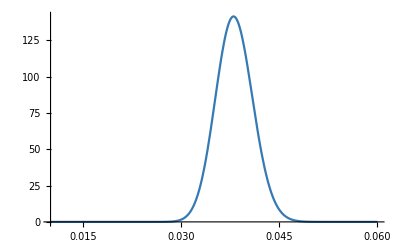

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
AbsoluteTiming[
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;
naivep=fracpop.(datacities[[All,4]]/(datacities[[All,3]]+1)); (* +1 to avoid error due to cities with 0 tests *)
{minp,maxp}=Rationalize[{Max[0,naivep-7/100],Min[1,naivep+8/100]},10^-4];

meanvartab=Table[newmeanvari[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint,V->varjoint};
finalpostbeta[p_]:=beta[p,bestα,bestβ];
]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazilround3=Plot[finalpostbeta[p-ptrue[0]],{p,.01,.06},PlotRange->All,PlotStyle->color1]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound3=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint,μjoint+4 √varjoint]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil3=Round[Join[ptabBrazilRound3,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound3=errorfun[{ptabBrazilRound3[[1;;4]]}][[1]]
```

{0.038,0.0327,0.0437,0.95}

{0.037991696937432040429515705,0.03809251241484491858454706563419,0.032652371241443132525154827,0.043718090101408656040421643,0.94999999379062402774896545}

{0.038,0.0381,0.0327,0.0437,0.95,298.312,5658.88,0.0028}

3.80.50.6

## Analysis

```mathematica
totround1+totround2+totround3
```

89397

### Prevalence Plot in States

```mathematica
ptabstatesRound1=Import[dir<>"prob-tab-states-FPR1.00%-round1-v4.csv","CSV"];
ptabstatesRound2=Import[dir<>"prob-tab-states-FPR1.00%-round2-v4.csv","CSV"];
ptabstatesRound3=Import[dir<>"prob-tab-states-FPR1.00%-round3-v4.csv","CSV"];
errortabstatesRound1=errorfun[ptabstatesRound1];
errortabstatesRound2=errorfun[ptabstatesRound2];
errortabstatesRound3=errorfun[ptabstatesRound3];
```

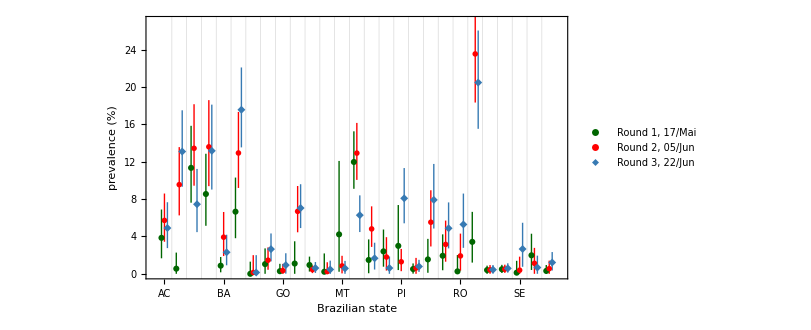

```mathematica
ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundENalt=ListPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,27}},FrameStyle->24,FrameLabel->{"Brazilian state","prevalence  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Automatic,{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

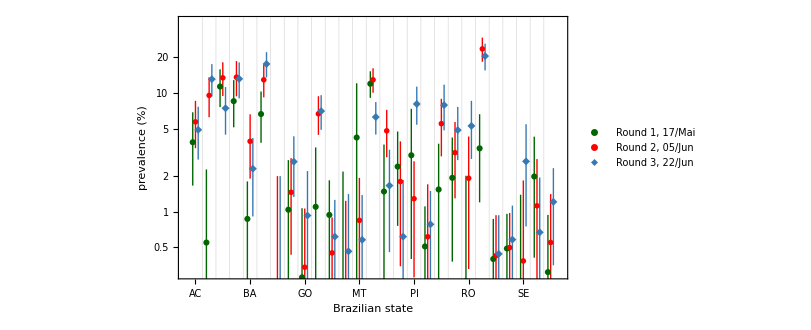

```mathematica
ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundENlog=ListLogPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{.3,40}},FrameStyle->24,FrameLabel->{"Brazilian state","prevalence  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Automatic,{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

### IFR calculation as inverse of a Beta

```mathematica
DFnyes=datacities3rounds[[27,6;;8]]
DFntot=datacities3rounds[[27,3;;5]]
```

{0,2,2}

{240,250,250}

```mathematica
dirIFR="results\\run15\\";
βshift=ptrue[0];
invbeta[pd_,α_,β_,x_]:=Piecewise[{{(pd (pd/x-βshift)^α (1-pd/x+βshift)^β Gamma[α+β])/((pd-x βshift) (pd-x (1+βshift)) (-1+BetaRegularized[-βshift,α,β]) Gamma[α] Gamma[β]),pd<x+x βshift},{0,pd≥x+x βshift}}];
invbetaCDFfull[pd_,α_,β_,x_]:=Piecewise[{{(-Gamma[α] Gamma[β]+Beta[pd/x-βshift,α,β] Gamma[α+β])/((-1+BetaRegularized[-βshift,α,β]) Gamma[α] Gamma[β]),pd<x+x βshift}},0];
invbetaCDF[pd_,α_,β_,x_]:=(-Gamma[α] Gamma[β]+Beta[pd/x-βshift,α,β] Gamma[α+β])/((-1+BetaRegularized[-βshift,α,β]) Gamma[α] Gamma[β]); (* x > pd/(1+βshift) *)
```

```mathematica
ptabstatesRound1=Import[dir<>"prob-tab-states-FPR1.00%-round1-v4.csv","CSV"];
ptabstatesRound2=Import[dir<>"prob-tab-states-FPR1.00%-round2-v4.csv","CSV"];
ptabstatesRound3=Import[dir<>"prob-tab-states-FPR1.00%-round3-v4.csv","CSV"];
```

```mathematica
approxmedian=(ptabstatesRound1[[All,-3]]-1/3)/(ptabstatesRound1[[All,-3]]+ptabstatesRound1[[All,-2]]-2/3)+ptrue[0]
approxmedian=InverseBetaRegularized[1/2,ptabstatesRound1[[All,-3]],ptabstatesRound1[[All,-2]]]+ptrue[0]
ptabstatesRound1[[All,2]]
(approxmedian-ptabstatesRound1[[All,2]])/ptabstatesRound1[[All,2]]
```

{0.0406867,0.00738183,0.115407,0.0877606,0.00929054,0.068599,0.000455825,0.0120601,0.00337673,0.013692,0.00993341,0.00450858,0.052494,0.120781,0.0170063,0.0257977,0.034568,0.00540833,0.0175435,0.021222,0.00452234,0.036735,0.00423453,0.00507885,0.00239321,0.0217379,0.00349793}

{0.0406915,0.00739029,0.115409,0.0877641,0.00929125,0.0686023,0.000463168,0.0120656,0.0033778,0.0137061,0.00993399,0.00452384,0.0525824,0.120782,0.0170144,0.025802,0.0345926,0.00540867,0.0175508,0.0212277,0.00453334,0.0367422,0.00423471,0.00507897,0.00239818,0.0217436,0.00349844}

{0.0407,0.0085,0.1154,0.0878,0.0093,0.0686,0.0039,0.0123,0.0041,0.0143,0.0099,0.0071,0.0528,0.1208,0.0172,0.0258,0.0347,0.0055,0.0177,0.0213,0.0067,0.0367,0.0043,0.0051,0.0046,0.0218,0.0039}

{-0.000208738,-0.130554,0.0000799495,-0.000408772,-0.000940337,0.0000334924,-0.881239,-0.0190606,-0.176147,-0.0415317,0.00343359,-0.36284,-0.00412154,-0.000150076,-0.0107893,0.0000782748,-0.00309433,-0.0166049,-0.00842704,-0.00339327,-0.323382,0.0011507,-0.0151836,-0.00412352,-0.478656,-0.00258736,-0.102964}

```mathematica
ptabstatesRound1b=Import[dir<>"prob-tab-states-FPR1.00%-round1-exact-v2.csv","CSV"];
ilisteff=ptabstatesRound1b[[All,1]]
Round[ptabstatesRound1b[[All,2;;]],.00001]
ptabstatesRound1[[All]]
```

{1,2,3,4,7,8,10,12,13,15,16,20,21,22,25,27}

{{0.03836,0.0407,0.01662,0.06911,0.95},{0.00434,0.00862,0.00014,0.02457,0.95},{0.11324,0.11549,0.07587,0.15922,0.95},{0.08536,0.08785,0.05119,0.12909,0.95},{0.,0.00339,0.,0.01461,0.95},{0.00901,0.01209,0.,0.02953,0.95346},{0.0092,0.0141,0.,0.0379,0.9517},{0.00271,0.00655,0.00013,0.02346,0.95},{0.03518,0.053,0.,0.1332,0.9537},{0.01318,0.01689,0.,0.03896,0.95453},{0.02363,0.02578,0.00788,0.04758,0.95},{0.01786,0.02127,0.,0.04394,0.95839},{0.0025,0.00646,0.00007,0.02203,0.95},{0.03406,0.03676,0.01202,0.06652,0.95},{0.00155,0.00444,0.00004,0.01587,0.95},{0.00288,0.00417,0.00038,0.01087,0.95}}

{{0.0385,0.0407,0.0166,0.0688,0.95,14.754,259.967,0.0136},{0.0055,0.0085,0.,0.0227,0.95,7.0232,339.999,0.0073},{0.1134,0.1154,0.0761,0.1584,0.95,31.9856,217.246,0.0211},{0.0854,0.0878,0.0514,0.1285,0.95,23.0465,205.45,0.0199},{0.0087,0.0093,0.0016,0.018,0.95,24.3716,1108.91,0.0043},{0.0665,0.0686,0.0381,0.103,0.95,21.6422,243.625,0.0168},{0.,0.0039,0.,0.013,0.95,6.0949,459.627,0.0048},{0.0104,0.0123,0.,0.0272,0.95,9.6431,379.039,0.0078},{0.0028,0.0041,0.,0.0107,0.95,17.1422,1081.43,0.0036},{0.011,0.0143,0.,0.0348,0.95,6.3002,227.218,0.0104},{0.0094,0.0099,0.0024,0.0184,0.95,27.3621,1209.38,0.0042},{0.0022,0.0071,0.,0.0218,0.95,4.9318,275.417,0.0074},{0.0422,0.0528,0.0022,0.1208,0.95,4.0514,54.3249,0.0329},{0.1197,0.1208,0.091,0.1525,0.95,61.9267,402.845,0.0157},{0.0148,0.0172,0.0006,0.0368,0.95,8.6406,279.083,0.01},{0.024,0.0258,0.0076,0.0474,0.95,13.2675,330.2,0.0104},{0.0299,0.0347,0.004,0.0736,0.95,6.3654,124.02,0.0188},{0.0051,0.0055,0.0002,0.0111,0.95,31.8519,1786.34,0.0031},{0.0154,0.0177,0.0011,0.0374,0.95,9.1648,291.111,0.0099},{0.0193,0.0213,0.0038,0.0422,0.95,10.9359,309.517,0.0101},{0.0026,0.0067,0.,0.0201,0.95,5.7519,324.201,0.0068},{0.0342,0.0367,0.012,0.0663,0.95,11.7434,223.369,0.0142},{0.004,0.0043,0.,0.0087,0.95,42.4105,2560.8,0.0025},{0.0049,0.0051,0.0009,0.0096,0.95,53.6953,3083.69,0.0023},{0.0012,0.0046,0.,0.0139,0.95,7.8563,517.923,0.005},{0.0198,0.0218,0.0041,0.0429,0.95,11.0426,307.68,0.0102},{0.0031,0.0039,0.,0.0094,0.95,24.6835,1553.98,0.0031}}

```mathematica
(*Plot[invbeta[1/1000,αtab[[1]],βtab[[1]],x],{x,0,.07},PlotRange->All]
Plot[invbetaCDF[1./1000,1.αtab[[1]],1.βtab[[1]],x],{x,0,.07},PlotRange->All]*)
```

```mathematica
invbetapdftab=Table[
cdf[x_]=invbetaCDF[pdvec[[i]],αtab[[i]],βtab[[i]],x];
xmedian=x/.FindRoot[cdf[x]==50/100,{x,IFRvec[[i]],2 10^-4,1},PrecisionGoal->5,AccuracyGoal->5];
pdf[x_]=invbeta[pdvec[[i]],αtab[[i]],βtab[[i]],x];
Simplify[pdf[x],x>pdvec[[i]]/(1+βshift)]
,{i,1,Length[ptabstatesRoundX]}];
```

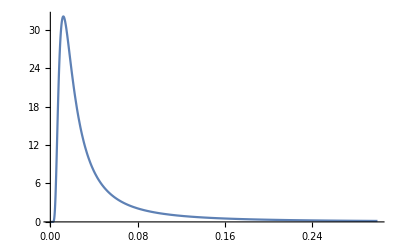

```mathematica
Plot[invbetapdftab[[2]],{x,pdvec[[2]]/(1+βshift),.3},PlotRange->All]
```

```mathematica
Monitor[
Do[
ptabstatesRoundX=Import[dir<>"prob-tab-states-FPR1.00%-round"<>ToString[round]<>"-v4.csv","CSV"];
valedata=Import[dirIFR<>"15-ztab-a2-m2-f"<>ToString[round]<>".txt","CSV"];
pdvec=valedata[[2;;All,8]];
IFRvec=valedata[[2;;All,4]];
αtab=ptabstatesRoundX[[All,6]];
βtab=ptabstatesRoundX[[All,7]];
Print[1.{αtab[[7]],βtab[[7]]}];
αtab[[7]]=DFnyes[[round]]+1.001; βtab[[7]]=DFntot[[round]](1-FNR-FPR)-DFnyes[[round]]+1.; 
Print[1.{αtab[[7]],βtab[[7]]}];(* DF has only 1 city -- city approx is better *)
IFRtab=Table[
xlowerlimit=pdvec[[i]]/(1+βshift);
cdf[x_]=Simplify[invbetaCDF[pdvec[[i]],αtab[[i]],βtab[[i]],x],x>xlowerlimit];
xmedian=x/.FindRoot[cdf[x]==50/100,{x,IFRvec[[i]],2 10^-4,1},PrecisionGoal->5,AccuracyGoal->5];
pdf[x_]=Simplify[invbeta[pdvec[[i]],αtab[[i]],βtab[[i]],x],x>xlowerlimit];

findmax=NMaximize[{pdf[x],xlowerlimit≤x<13/10 xmedian},x];
zmax=findmax[[1]];
xxmax=x/.findmax[[2]];

zrange=Range[zmax/1000,zmax/3,zmax/300];
areatab=Table[
xmintemp=x/.FindRoot[pdf[x]==zrange[[j]],{x,7/10xxmax,xlowerlimit,xxmax}];
xmaxtemp=x/.FindRoot[pdf[x]==zrange[[j]],{x,13/10xxmax,xxmax,1}];
areaunder=cdf[xmaxtemp]-cdf[xmintemp];
{zrange[[j]],areaunder}
,{j,1,Length[zrange]}
];
areafun=Interpolation[areatab,InterpolationOrder->1];
z95=z/.FindRoot[areafun[z]==95/100,{z,zmax/10,zmax/1000,zmax/3}];
xmin=x/.NMinimize[{(pdf[x]-z95)^2,xlowerlimit<x<xxmax},x][[2]];
xmax=x/.NMinimize[{(pdf[x]-z95)^2,xxmax<x<1},x][[2]];
crosscheck=NIntegrate[pdf[x],{x,xmin,xmax}];
If[.945<crosscheck<.955,Null,Print["crosscheck error!  i = "<>ToString[i]<>";  CI = "<>ToString[crosscheck]<>"; and Max CDF = "<>ToString[cdf[1.]]]];

(*Print[{i,xmedian,xmin,xmax}];*)
{statesnames[[i]],xxmax,xmedian,xmin,xmax,crosscheck}
,{i,1,Length[ptabstatesRoundX]}];
Export["IFR-95CI-MQ-round"<>ToString[round]<>"-v5.txt",IFRtab,"CSV"]
,{round,1,3}],
{round,i}]
```

{6.0949,459.627}

{1.001,202.12}

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.0000502517}. Try perturbing the initial point(s).

General::munfl: Exp[-6864.85+634.979 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.0000502517}. Try perturbing the initial point(s).

General::munfl: Exp[-6864.85+634.979 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.0000502517}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

General::munfl: Exp[-6864.85+634.979 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{5.00924,297.832}

{3.001,208.5}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5.00924,297.832}

{3.001,208.5}

FindRoot::reged: The point {1.} is at the edge of the search region {0.0154748,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.} is at the edge of the search region {0.0644105,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.} is at the edge of the search region {0.0363663,1.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

```mathematica
findmax=NMaximize[{pdf[x],xlowerlimit≤x<13/10 xmedian},x]
zmax=findmax[[1]];
xxmax=x/.findmax[[2]];

zrange=Range[zmax/1000,zmax/3,zmax/300];
areatab=Table[
xmintemp=x/.FindRoot[pdf[x]==zrange[[j]],{x,7/10xxmax,xlowerlimit,xxmax}];
xmaxtemp=x/.FindRoot[pdf[x]==zrange[[j]],{x,13/10xxmax,xxmax,1}];
areaunder=cdf[xmaxtemp]-cdf[xmintemp];
{zrange[[j]],areaunder}
,{j,1,Length[zrange]}
];
areafun=Interpolation[areatab,InterpolationOrder->1];
z95=z/.FindRoot[areafun[z]==95/100,{z,zmax/10,zmax/500,zmax/3}]
xmin=x/.NMinimize[{(pdf[x]-z95)^2,xlowerlimit<x<xxmax},x][[2]];
xmax=x/.NMinimize[{(pdf[x]-z95)^2,xxmax<x<1},x][[2]];
{xmin,xmax}
```

{90.9995,{x→0.00682455}}

1.34989

{0.00257831,0.0498495}

```mathematica
z95
{xlowerlimit,xmin,xmax}
NIntegrate[pdf[x],{x,xmin,xmax}]
cdf[xmax]-cdf[xmin]
```

0.0662094

{0.000492715,0.0110586,0.774739}

0.94954

0.94954

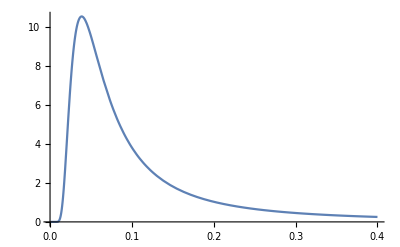

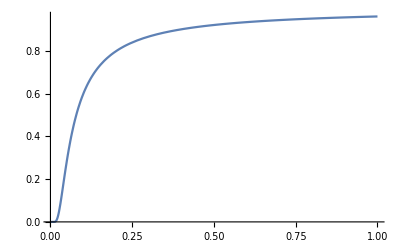

```mathematica
Plot[pdf[x],{x,0,.4},PlotRange->All]
Plot[cdf[x],{x,0,1},PlotRange->All]
```

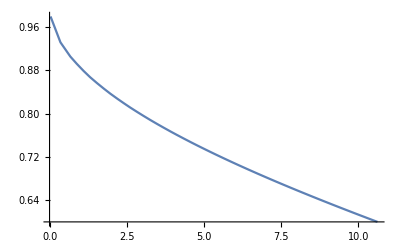

```mathematica
Plot[areafun[x],{x,areafun[[1,1,1]],areafun[[1,1,2]]}]
```

### IFR calculation as inverse of a Beta for the whole country

```mathematica
Clear[ifrcountry]
maxifr=0.017;
```

```mathematica
ifrcountry[ifrfun_]:=Module[{},
findmax=NMaximize[{ifrfun[x],.004≤x<maxifr},x];
zmax=findmax[[1]];
xxmax=x/.findmax[[2]];
zrange=Range[zmax/1000,zmax/3,zmax/300];
areatab=Table[
xmintemp=x/.FindRoot[ifrfun[x]==zrange[[j]],{x,9/10xxmax,.004,xxmax}];
xmaxtemp=x/.FindRoot[ifrfun[x]==zrange[[j]],{x,11/10xxmax,xxmax,maxifr}];
areaunder=NIntegrate[ifrfun[x],{x,xmintemp,xmaxtemp}];
{zrange[[j]],areaunder}
,{j,1,Length[zrange]}
];
areafun=Interpolation[areatab,InterpolationOrder->1];
z95=z/.FindRoot[areafun[z]==95/100,{z,zmax/10,zmax/1000,zmax/3}];
xmin=x/.NMinimize[{(ifrfun[x]-z95)^2,.004<x<xxmax},x][[2]];
xmax=x/.NMinimize[{(ifrfun[x]-z95)^2,xxmax<x<maxifr},x][[2]];
crosscheck=NIntegrate[ifrfun[x],{x,xmin,xmax}];
{xxmax,ifr,xmin,xmax,crosscheck}]
```

```mathematica
(* Round 1 *)
fd=0.0002155;σfd=0.03288 fd;
fa=0.0259;σfa=0.0030;
dist=TransformedDistribution[y/x,{x\[Distributed]NormalDistribution[fa,σfa],y\[Distributed]NormalDistribution[fd,σfd]}]
ifr=fd/fa
σifr=√((σfd/fa)^2+(σfa fd/fa^2)^2)
```

TransformedDistribution[x2/x1,{x1\[Distributed]NormalDistribution[0.0259,0.003],x2\[Distributed]NormalDistribution[0.0002155,7.08564×10^-6]}]

0.00832046

0.00100184

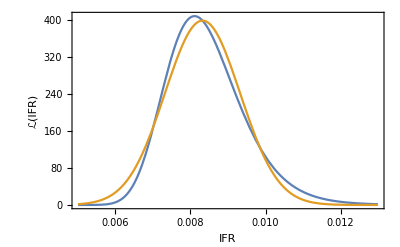

```mathematica
map=ParallelMap[{#,PDF[dist,#]}&,Range[.004,maxifr,.0001]];
ifrfun1=Interpolation[map];
Plot[{ifrfun1[x],PDF[NormalDistribution[ifr,σifr],x]},{x,.005,.013},Frame->True,FrameStyle->15,FrameLabel->{"IFR","ℒ(IFR)"},PlotRange->All]
```

```mathematica
ifrcountry[ifrfun1]
```

{0.00810803,0.00832046,0.00652892,0.0105588,0.950001}

```mathematica
μjoint+ptrue[0]
√varjoint
```

-5/419+μjoint

√varjoint

```mathematica
(* Round 2 *)
fd=0.00035198;σfd=0.020988 fd;
fa=0.03801;σfa=0.00301;
dist=TransformedDistribution[y/x,{x\[Distributed]NormalDistribution[fa,σfa],y\[Distributed]NormalDistribution[fd,σfd]}];
ifr=fd/fa
σifr=√((σfd/fa)^2+(σfa fd/fa^2)^2)
(σfa/fa)/(σfd/fd)
```

0.00926019

0.00075863

3.77309

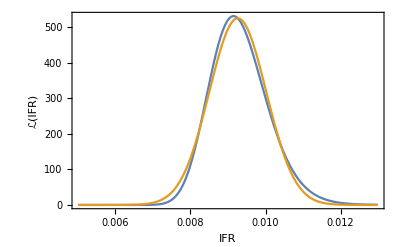

```mathematica
map=ParallelMap[{#,PDF[dist,#]}&,Range[.004,maxifr,.0001]];
ifrfun2=Interpolation[map];
Plot[{ifrfun2[x],PDF[NormalDistribution[ifr,σifr],x]},{x,.005,.013},Frame->True,FrameStyle->15,FrameLabel->{"IFR","ℒ(IFR)"},PlotRange->All]
```

```mathematica
ifrcountry[ifrfun2]
```

{0.00914681,0.00926019,0.00786693,0.010876,0.950001}

```mathematica
μjoint+ptrue[0]
√varjoint
```

0.0381428007380944554087713714934

0.00282554247214908943594040058632

```mathematica
(* Round 3 *)
fd=0.00046918;σfd=0.01453 fd;
fa=0.0381;σfa=0.002826;
dist=TransformedDistribution[y/x,{x\[Distributed]NormalDistribution[fa,σfa],y\[Distributed]NormalDistribution[fd,σfd]}];
ifr=fd/fa
σifr=√((σfd/fa)^2+(σfa fd/fa^2)^2)
```

0.0123144

0.000930762

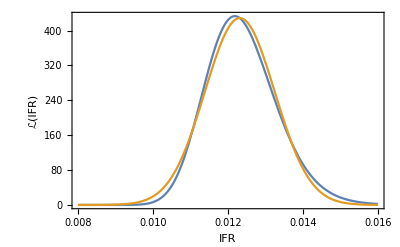

```mathematica
map=ParallelMap[{#,PDF[dist,#]}&,Range[.004,maxifr,.0001]];
ifrfun3=Interpolation[map];
Plot[{ifrfun3[x],PDF[NormalDistribution[ifr,σifr],x]},{x,.008,.016},Frame->True,FrameStyle->15,FrameLabel->{"IFR","ℒ(IFR)"},PlotRange->All]
```

```mathematica
ifrcountry[ifrfun3]
```

{0.012182,0.0123144,0.0106005,0.0142869,0.95}

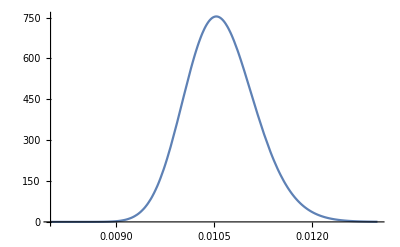

```mathematica
ifr123[x_]=ifrfun1[x]ifrfun2[x]ifrfun3[x];
norm=1/NIntegrate[ifr123[x],{x,.004,.02}];
ifr123[x_]=norm ifr123[x];
Plot[ifr123[x],{x,.008,.013},PlotRange->All]
```

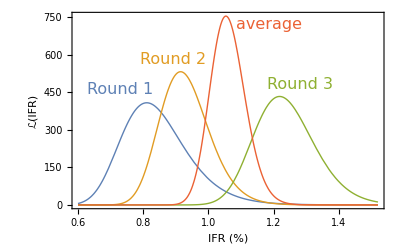

brazil-ifr-plot.pdf

```mathematica
colors=ColorData[97,"ColorList"];
pifr=Plot[{ifrfun1[x/100],ifrfun2[x/100],ifrfun3[x/100],ifr123[x/100]},{x,.6,1.52},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","ℒ(IFR)"},PlotRange->All,PlotStyle->Thick];
sifr=Show[pifr,
Graphics[Text[Style["Round 1",16,colors[[1]]],{.73,460}]],Graphics[Text[Style["Round 2",16,colors[[2]]],{.89,580}]],Graphics[Text[Style["Round 3",16,colors[[3]]],{1.28,480}]],Graphics[Text[Style["average",16,colors[[4]]],{1.185,720}]]]
Export["brazil-ifr-plot.pdf",sifr]
```

```mathematica
ifrcountry[ifr123]
```

{0.0105354,0.0123144,0.00958633,0.0116788,0.950001}

### Combining all Rounds

```mathematica
Monitor[
IFRpdftabrounds=Table[
ptabstatesRoundX=Import[dir<>"prob-tab-states-FPR1.00%-round"<>ToString[round]<>"-v4.csv","CSV"];
valedata=Import[dirIFR<>"15-ztab-a2-m2-f"<>ToString[round]<>".txt","CSV"];
pdvec=valedata[[2;;All,8]];
IFRvec=valedata[[2;;All,4]];
αtab=ptabstatesRoundX[[All,6]];
βtab=ptabstatesRoundX[[All,7]];
αtab[[7]]=DFnyes[[round]]+1.001; βtab[[7]]=DFntot[[round]](1-FNR-FPR)-DFnyes[[round]]+1.; 

tab=Table[
xlowerlimit=pdvec[[i]]/(1+βshift);
cdf[x_]=Simplify[invbetaCDF[pdvec[[i]],αtab[[i]],βtab[[i]],x],x>xlowerlimit];
xmedian=x/.FindRoot[cdf[x]==50/100,{x,IFRvec[[i]],2 10^-4,1},PrecisionGoal->5,AccuracyGoal->5];
pdf[x_]=Simplify[invbeta[pdvec[[i]],αtab[[i]],βtab[[i]],x],x>xlowerlimit];
{xlowerlimit,pdf[x]}
,{i,1,Length[ptabstatesRoundX]}];

tab

,{round,1,3}];,
{round,i}]
Dimensions[IFRpdftabrounds]
```

{3,27,2}

```mathematica
Monitor[
IFRtabcomb=Table[
xlowerlimittot=Max[{IFRpdftabrounds[[1,i,1]],IFRpdftabrounds[[2,i,1]],IFRpdftabrounds[[3,i,1]]}];
pdftot[x_]=IFRpdftabrounds[[1,i,2]]IFRpdftabrounds[[2,i,2]]IFRpdftabrounds[[3,i,2]];
norm=1/NIntegrate[pdftot[x],{x,xlowerlimittot,1}];
pdftot[x_]=norm pdftot[x];

findmax=NMaximize[{pdftot[x],xlowerlimittot≤x<4/10},x];
zmax=findmax[[1]];
xxmax=x/.findmax[[2]];

xmedianfun[y_]:=NIntegrate[pdftot[x],{x,xlowerlimittot,y}];
(*xmedian=y/.NMinimize[{(xmedianfun[y]-1/2)^2,2/3xxmax<y<3/10},y][[2]];*)
xmedian=y/.FindRoot[xmedianfun[y]==1/2,{y,xxmax,3/4xxmax,3/10}];

zrange=Range[zmax/1000,zmax/3,zmax/30];
areatab=Table[
xmintemp=x/.FindRoot[pdftot[x]==zrange[[j]],{x,7/10xxmax,xlowerlimittot,xxmax}];
xmaxtemp=x/.FindRoot[pdftot[x]==zrange[[j]],{x,13/10xxmax,xxmax,1}];
areaunder=NIntegrate[pdftot[x],{x,xmintemp,xmaxtemp}];
{zrange[[j]],areaunder}
,{j,1,Length[zrange]}
];
areafun=Interpolation[areatab,InterpolationOrder->1];
z95=z/.FindRoot[areafun[z]==95/100,{z,zmax/10,zmax/1000,zmax/3}];
(*xmin=x/.FindRoot[pdf[x]==z95,{x,8/10xxmax,xlowerlimit,xxmax}];
xmax=x/.FindRoot[pdf[x]==z95,{x,12/10xxmax,xxmax,1}];*)
xmin=x/.NMinimize[{(pdftot[x]-z95)^2,xlowerlimittot<x<xxmax},x][[2]];
xmax=x/.NMinimize[{(pdftot[x]-z95)^2,xxmax<x<1},x][[2]];
crosscheck=NIntegrate[pdftot[x],{x,xmin,xmax}];
If[.945<crosscheck<.955,Null,Print["crosscheck error! CI = "<>ToString[crosscheck]]];

{statesnames[[i]],xxmax,xmedian,xmin,xmax,crosscheck}
,{i,1,Length[ptabstatesRoundX]}];

Export["IFR-95CI-MQ-combined-v5.txt",IFRtabcomb,"CSV"]
,{i}]
```

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

IFR-95CI-MQ-combined-v5.txt

### IFR Plot

```mathematica
dirIFR="results\\run15\\";
dirIFR2="miguelito\\";
ϵ=.2;
```

```mathematica
data1=Import[dirIFR2<>"IFR-95CI-MQ-round1-v5.txt","CSV"][[All,2;;]];
IFRstatesRound1=Thread[{Range[1,27]-ϵ,errorfun[data1]}];
data2=Import[dirIFR2<>"IFR-95CI-MQ-round2-v5.txt","CSV"][[All,2;;]];
IFRstatesRound2=Thread[{Range[1,27],errorfun[data2]}];
data3=Import[dirIFR2<>"IFR-95CI-MQ-round3-v5.txt","CSV"][[All,2;;]];
IFRstatesRound3=Thread[{Range[1,27]+ϵ,errorfun[data3]}];
```

```mathematica
data123=Import[dirIFR2<>"IFR-95CI-MQ-combined-v5.txt","CSV"][[All,2;;]];
IFRstatescombined=Thread[{Range[1,27],errorfun[data123]}];
```

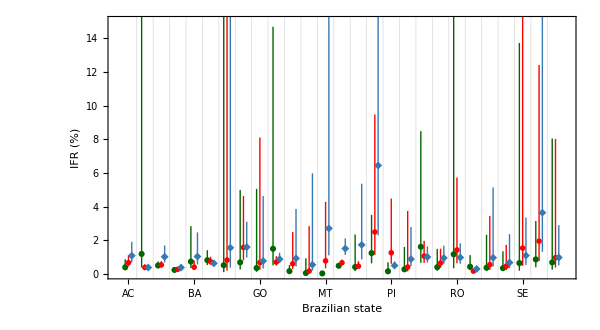

```mathematica
lpstatesIFREN=ListPlot[{IFRstatesRound1,IFRstatesRound2,IFRstatesRound3},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,15}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Automatic,{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

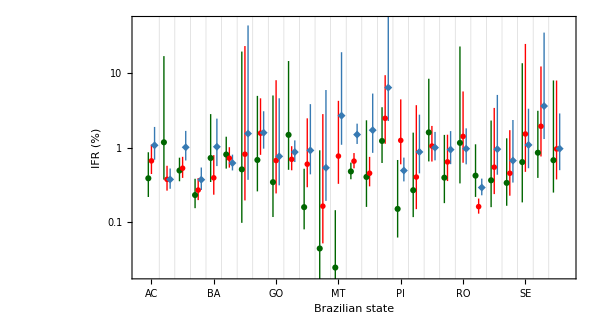

```mathematica
lpstatesIFRENlog=ListLogPlot[{IFRstatesRound1,IFRstatesRound2,IFRstatesRound3(*,IFRstatescombined*)},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{.02,50}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Green,.6],Red,color1,Black},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1,Black},PlotMarkers->{Automatic,"OpenMarkers",Automatic,Automatic},FrameTicks->{{Join[Table[{i,""},{i,.005,.01,.001}],Table[{i,""},{i,.01,.1,.01}],Table[{i,""},{i,.1,1,.1}],Table[{i,""},{i,1,10,1}],Table[{i,""},{i,10,100,10}],{.01,.1,1,10}],
Join[Table[{i,""},{i,.01,.1,.01}],Table[{i,""},{i,.1,1,.1}],Table[{i,""},{i,1,10,1}],Table[{i,""},{i,10,100,10}]]},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

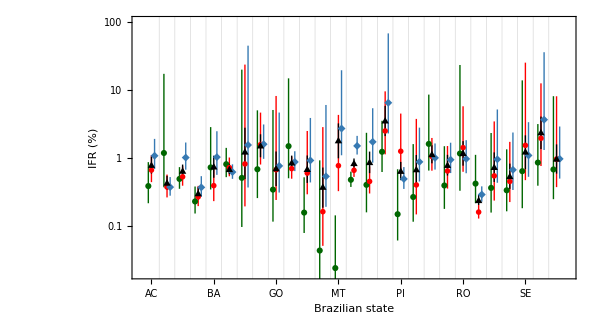

```mathematica
lpstatesIFRENlogfull=ListLogPlot[{IFRstatesRound1,IFRstatesRound2,IFRstatesRound3,IFRstatescombined},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{.02,100}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Green,.6],Red,color1,Black},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1,Black},PlotMarkers->{Automatic,"OpenMarkers",Automatic,Automatic},FrameTicks->{{Join[Table[{i,""},{i,.005,.01,.001}],Table[{i,""},{i,.01,.1,.01}],Table[{i,""},{i,.1,1,.1}],Table[{i,""},{i,1,10,1}],Table[{i,""},{i,10,100,10}],{.01,.1,1,10}],
Join[Table[{i,""},{i,.01,.1,.01}],Table[{i,""},{i,.1,1,.1}],Table[{i,""},{i,1,10,1}],Table[{i,""},{i,10,100,10}]]},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

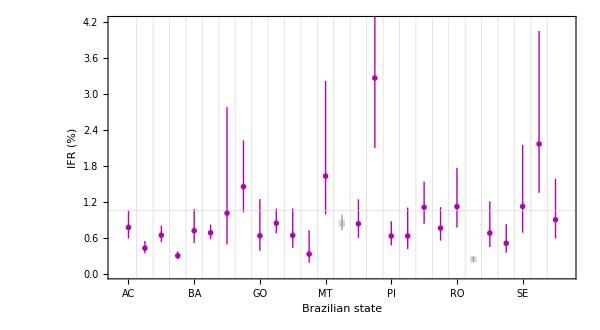

```mathematica
lpstatesIFRcombined=ListPlot[{IFRstatescombined[[Delete[Range[1,27],{{14},{22}}]]],IFRstatescombined[[{14,22}]]},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,4.2}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Magenta,.3],Opacity[.3,Gray],Black},
IntervalMarkersStyle->{Darker[Magenta,.3],Opacity[.8,Gray]},PlotMarkers->{"OpenMarkers",Automatic,Automatic},FrameTicks->{{Automatic,Automatic},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},
FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],{1.05}},GridLinesStyle->{Lighter[Gray,.7],Red}]
```

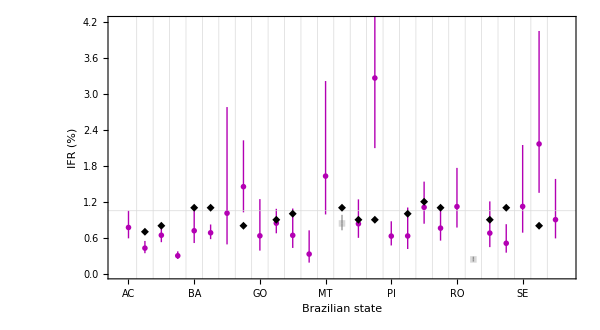

```mathematica
lpstatesIFRcombinedimperial=ListPlot[{IFRstatescombined[[Delete[Range[1,27],{{14},{22}}]]],IFRstatescombined[[{14,22}]],imperiallist},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,4.2}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Magenta,.3],Opacity[.3,Gray],Black},
IntervalMarkersStyle->{Darker[Magenta,.3],Opacity[.8,Gray]},PlotMarkers->{"OpenMarkers",Automatic,Automatic},FrameTicks->{{Automatic,Automatic},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},
FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],{1.05}},GridLinesStyle->{Lighter[Gray,.7],Red}]
```

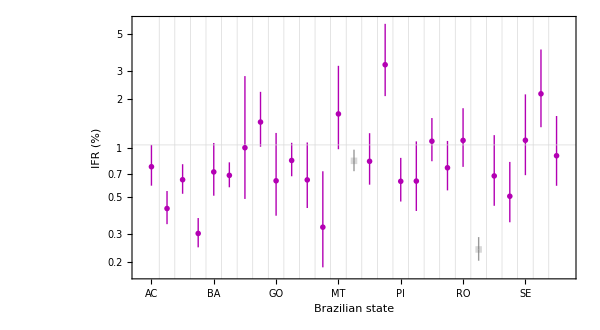

```mathematica
lpstatesIFRcombinedlog=ListLogPlot[{IFRstatescombined[[Delete[Range[1,27],{{14},{22}}]]],IFRstatescombined[[{14,22}]]},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{.17,6}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Magenta,.3],Opacity[.3,Gray]},
IntervalMarkersStyle->{Darker[Magenta,.3],Opacity[.8,Gray]},PlotMarkers->{"OpenMarkers",Automatic,Automatic},FrameTicks->{{Automatic,Automatic},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},
FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],{1.05}},GridLinesStyle->{Lighter[Gray,.7],Red}]
```

```mathematica
Export["15-state-IFR-FPR1-full-EN.pdf",lpstatesIFREN]
Export["15-state-IFR-FPR1-full-log-EN.pdf",lpstatesIFRENlog]
Export["15-state-IFR-FPR1-full-combined.pdf",lpstatesIFRcombined]
Export["15-state-IFR-FPR1-full-log-combined.pdf",lpstatesIFRcombinedlog]
```

15-state-IFR-FPR1-full-EN.pdf

15-state-IFR-FPR1-full-log-EN.pdf

15-state-IFR-FPR1-full-combined.pdf

15-state-IFR-FPR1-full-log-combined.pdf

### Combining Brazil’s IFR in the 3 rounds

```mathematica
IFR={0.83,0.93,1.23};
σIFR={.17,.10,.12};
```

```mathematica
ifr1=Import["results\\run101\\101-ztab-a1-m2-f1.txt","CSV"][[2,4;;5]];
ifr2=Import["results\\run101\\101-ztab-a1-m2-f2.txt","CSV"][[2,4;;5]];
ifr3=Import["results\\run101\\101-ztab-a1-m2-f3.txt","CSV"][[2,4;;5]];
IFR=100{ifr1[[1]],ifr2[[1]],ifr3[[1]]}
σIFR=100{ifr1[[2]],ifr2[[2]],ifr3[[2]]}
```

{0.828829,0.926257,1.23144}

{0.0994414,0.0756654,0.0922509}

```mathematica
ndeaths={26623.3,45494.9,62843.3};
corr12=0 √(ndeaths[[1]]/ndeaths[[2]]);
corr13=0 √(ndeaths[[1]]/ndeaths[[3]]);
corr23=0 √(ndeaths[[2]]/ndeaths[[3]]);
{corr12,corr13,corr23}
```

{0.,0.,0.}

```mathematica
(IFR.σIFR^-2)/Total[σIFR^-2]
Total[σIFR^-2]^(-1/2)
```

0.992386

0.0504243

```mathematica
cov=Table[0,{i,3},{j,3}];
Table[cov[[i,i]]=σIFR[[i]]^2,{i,3}];
cov[[1,2]]=corr12 σIFR[[1]] σIFR[[2]];
cov[[1,3]]=corr13 σIFR[[1]] σIFR[[3]];
cov[[2,3]]=corr23 σIFR[[2]] σIFR[[3]];
cov[[2,1]]=cov[[1,2]];cov[[3,1]]=cov[[1,3]];cov[[3,2]]=cov[[2,3]];
icov=Inverse[cov];
cov//MatrixForm
```

(0.0098886 | 0. | 0.
0. | 0.00572525 | 0.
0. | 0. | 0.00851022)

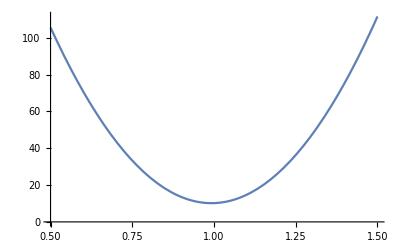

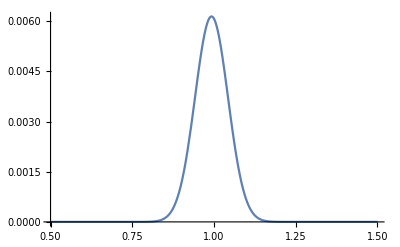

```mathematica
chisq[x_]:=(IFR-x).icov.(IFR-x);
Plot[chisq[x],{x,.5,1.5}]
Plot[Exp[-1/2 chisq[x]],{x,0.5,1.5},PlotRange->All]
```

```mathematica
chisqmin=FindMinValue[chisq[x],{x,1}];
xBF=x/.FindMinimum[chisq[x],{x,1}][[2]]
x1σmin=x/.FindRoot[chisq[x]==chisqmin+3.85,{x,.7},AccuracyGoal->5,PrecisionGoal->5];
x1σmax=x/.FindRoot[chisq[x]==chisqmin+3.85,{x,1.5},AccuracyGoal->5,PrecisionGoal->5];
{x1σmin,x1σmax}
xBF-x1σmin
x1σmax-xBF
Round[{xBF,xBF-x1σmin},.001]
```

0.992386

{0.893446,1.09133}

0.0989396

0.0989396

{0.992,0.099}

```mathematica
Round[{xBF,xBF-(xBF-x1σmin),xBF+(xBF-x1σmin)},.01]
Around[xBF,x1σmax-xBF]
```

{0.99,0.89,1.09}

0.990.10

```mathematica
norm=NIntegrate[Exp[-1/2 chisq[x]],{x,0,3}];
(1/norm)NIntegrate[Exp[-1/2 chisq[x]],{x,x1σmin,x1σmax}]
```

0.950254

```mathematica
Round[{xBF,xBF-x1σmin},.001]
```

{1.176,0.137}

```mathematica
data1=RandomReal[1,100000];
data2=RandomReal[1,100000];
data3=data1+data2;
```

```mathematica
√(1/2.)
```

0.707107

```mathematica
Correlation[data1,data2]
Correlation[data1,data3]
```

0.00364266

0.708028

### IFR Imperial Brazil Report 21

```mathematica
(* Estimates for 6/May/2020 *)
```

```mathematica
imperialstates={"SP","RJ","CE","PE","AM","PA","MA","BA","ES","PR","MG","PB","AL","RS","RN","SC"}
imperialpop={46.3,17.4,9.2,9.6,4.2,8.7,7.1,14.9,3.1,11.5,21.3,4.0,3.4,11.3,3.5,7.3};
imperialIFR=.1{7,8,11,11,8,9,10,11,9,9,10,12,11,9,11,8};
imperialIFR.imperialpop/Total[imperialpop]
```

{SP,RJ,CE,PE,AM,PA,MA,BA,ES,PR,MG,PB,AL,RS,RN,SC}

0.900055

```mathematica
imperial=Thread[{imperialstates,imperialIFR}]
imperial=Sort[imperial]
k=1;
imperiallist=Reap[Table[If[statesnames[[i]]==imperial[[k,1]],Sow[{i,imperialIFR[[k]]}];k=Min[k+1,Length[imperial]];]
,{i,27}]][[2,1]]
```

{{SP,0.7},{RJ,0.8},{CE,1.1},{PE,1.1},{AM,0.8},{PA,0.9},{MA,1.},{BA,1.1},{ES,0.9},{PR,0.9},{MG,1.},{PB,1.2},{AL,1.1},{RS,0.9},{RN,1.1},{SC,0.8}}

{{AL,1.1},{AM,0.8},{BA,1.1},{CE,1.1},{ES,0.9},{MA,1.},{MG,1.},{PA,0.9},{PB,1.2},{PE,1.1},{PR,0.9},{RJ,0.8},{RN,1.1},{RS,0.9},{SC,0.8},{SP,0.7}}

{{2,0.7},{3,0.8},{5,1.1},{6,1.1},{8,0.8},{10,0.9},{11,1.},{14,1.1},{15,0.9},{16,0.9},{18,1.},{19,1.2},{20,1.1},{23,0.9},{24,1.1},{26,0.8}}